# Initialization

```mathematica
$FKKSRoot = NotebookDirectory[]<>"../";
$SolutionPath = $FKKSRoot<>"Solutions/";
PlotPath = $FKKSRoot<>"Plots/";
LogFile = $FKKSRoot<>"Logs/LogFile";
PlotFileExtension = ".png";
NumberofSlaveKernels = Automatic; (*Default should be Automatic*)

(*Import some helper functions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "HelperFunctions.wl"}]]

(*Setup xAct definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "xActSetup.wl"}]]

(*Setup Proca Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "KerrWithProca.wl"}]]

(*Setup Energy Momentum Definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "EnergyMomentum.wl"}]]

(*Setup MST Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "MSTSolver.wl"}]]

(*Setup Inhomogeneous Teukolsky Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "TeukolskySolver.wl"}]]

Off[PrintAsCharacter::argx];

NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
```

# Teukolsky Kinnersely projection consistency tests

## T_nn

```mathematica
SampleData = Import@FileNames["../Solutions/*.mx", NotebookDirectory[]][[2]];
rdom = SampleData["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#,data["Parameters", "χ"]]&;
PrintTemporary@Dynamic[$Messenger];
tnnSymbolic = {t,r,θ,ϕ}|->Evaluate@Tnn[SampleData, AsSymbolic->True];
tnnOptimized = Tnn[SampleData, AsOptimized->True];
tnnInterpolating = Tnn[SampleData, AsInterpolatingFunction->True];
```

```mathematica
(*Symbolic form of Tnn takes a very long time to calculate a single point, let alone plot, so we just verify the symbolic form agrees well with the Optimized form*)
With[{θpoint = π/2, radialpoint = 50},
Print["Fractional difference between Optimized form of Tnn and Symbolic form at (r,θ)=(50,π/2):"];
((tnnOptimized[0,radialpoint,θpoint,0]-tnnSymbolic[0,radialpoint,θpoint,0])/tnnSymbolic[0,radialpoint,θpoint,0])
]
```

```mathematica
(*Plot the fractional difference between the Optimized form of Tnn and the function that Interpolates Tnn*)
With[{θpoint = π/2, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tnn and the InterpolationFunction form at θ=π/2:"];
Plot[(tnnInterpolating[Ttest,r,θpoint,ϕtest]-tnnOptimized[Ttest,r,θpoint,ϕtest])/tnnOptimized[Ttest,r,θpoint,ϕtest], {r,1.44,rdom[[-1]]/1.5}, ImageSize->Medium, PlotRange->All]
]
```

## T_(m̄ m̄)

```mathematica
SampleData = Import@FileNames["../Solutions/*.mx", NotebookDirectory[]][[2]];
rdom = SampleData["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#,SampleData["Parameters", "χ"]]&;
PrintTemporary@Dynamic[$Messenger];
tmbmbSymbolic = {t,r,θ,ϕ}|->Evaluate@Tmbmb[SampleData, AsSymbolic->True];
tmbmbOptimized = Tmbmb[SampleData, AsOptimized->True];
tmbmbInterpolating = Tmbmb[SampleData, AsInterpolatingFunction->True];
```

```mathematica
(*Symbolic form of Tmbmb takes a very long time to calculate a single point, let alone plot, so we just verify the symbolic form agrees well with the Optimized form*)
With[{θpoint = π/2, radialpoint = 50, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tmbmb and Symbolic form at (r,θ)=(50,π/2):"];
((tmbmbOptimized[Ttest,radialpoint,θpoint,ϕtest]-tmbmbSymbolic[Ttest,radialpoint,θpoint,ϕtest])/tmbmbSymbolic[Ttest,radialpoint,θpoint,ϕtest])
]
```

```mathematica
(*Plot the fractional difference between the Optimized form of Tmbmb and the function that Interpolates Tnn*)
With[{θpoint = π/2, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tmbmb and the InterpolationFunction form at θ=π/2:"];
Plot[Abs@((tmbmbInterpolating[Ttest,r,θpoint,ϕtest]-tmbmbOptimized[Ttest,r,θpoint,ϕtest])/tmbmbOptimized[Ttest,r,θpoint,ϕtest]), {r,1.44,rdom[[-1]]/1.5}, ImageSize->Medium, PlotRange->All]
]
```

## T_(m̄ n)

```mathematica
SampleData = Import@FileNames["../Solutions/*.mx", NotebookDirectory[]][[2]];
rdom = SampleData["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#,data["Parameters", "χ"]]&;
PrintTemporary@Dynamic[$Messenger];
tmbnSymbolic = {t,r,θ,ϕ}|->Evaluate@Tmbn[SampleData, AsSymbolic->True];
tmbnOptimized = Tmbn[SampleData, AsOptimized->True];
tmbnInterpolating = Tmbn[SampleData, AsInterpolatingFunction->True];
```

```mathematica
(*Symbolic form of Tmbn takes a very long time to calculate a single point, let alone plot, so we just verify the symbolic form agrees well with the Optimized form*)
With[{θpoint = π/2, radialpoint = 50},
Print["Fractional difference between Optimized form of Tmbn and Symbolic form at (r,θ)=(50,π/2):"];
((tmbnOptimized[0,radialpoint,θpoint,0]-tmbnSymbolic[0,radialpoint,θpoint,0])/tmbnSymbolic[0,radialpoint,θpoint,0])
]
```

```mathematica
(*Plot the fractional difference between the Optimized form of Tmbn and the function that Interpolates Tnn*)
With[{θpoint = π/2, Ttest = RandomReal[{0,10}], ϕtest = RandomReal[{0,2*π}]},
Print["Fractional difference between Optimized form of Tmbn and the InterpolationFunction form at θ=π/2:"];
Plot[Abs@((tmbnInterpolating[Ttest,r,θpoint,ϕtest]-tmbnOptimized[Ttest,r,θpoint,ϕtest])/tmbnOptimized[Ttest,r,θpoint,ϕtest]), {r,1.44,rdom[[-1]]/1.5}, ImageSize->Medium, PlotRange->All]
]
```

# Comparison to Nils Code

## Function by Function

## Vector Field

#### Numerical

```mathematica
testsol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv3_10m1η0n0l0s-1χ9_10KMax4branch1.mx"];
radialSolution = testsol["Solution", "R"];
angularSolution = testsol["Solution", "S"];


NotebookEvaluate[NotebookDirectory[]<>"NilsFunctions.nb"];
GenerateNilsVectorField[testsol];

AupNils = Aupvector;
AdownNils = Adownvector;
AupNilsExplicit = OptimizedFunction[{t,r,θ,ϕ}, AupSimp/.solidentify/.parameters];
AdownNilsExplicit = OptimizedFunction[{t,r,θ,ϕ}, AdownSimp/.solidentify/.parameters];

ReprRule = {a->testsol["Parameters", "χ"]};
AupMe = FKKSProca[testsol, Optimized->True, RealPart->True, QuasiboundState->True];
With[{Ttest =RandomReal[{0,100}], RTest = RandomReal[{2,100}], θTest = RandomReal[{0,π}], ϕTest = RandomReal[{0,2*π}]},
Column[{
Row[{"(Ttest, Rtest, θtest, ϕtest) = "<>ToString@{Ttest, RTest, θTest, ϕTest}}],
Row[{
Row[{"My A^μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Interp A^μ: ", AupNils[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AupNils[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]]}]
}],
Row[{
Row[{"My A_μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,-sphericalchart}]/.ReprRule/.r[]->RTest/.θ[]->θTest, {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Interp A_μ: ", AdownNils[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AupNils[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}]/.ReprRule/.r->RTest/.θ->θTest, {i,0,3}]]}]
}],
Row[{
Row[{"My A^μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Explicit A^μ: ", AupNilsExplicit[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AupNilsExplicit[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}], {i,0,3}]]}]
}],
Row[{
Row[{"My A_μ: ", Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,-sphericalchart}]/.ReprRule/.r[]->RTest/.θ[]->θTest, {i,0,3}]//Column}],Spacer[20],
Row[{"Nils Explicit A_μ: ", AdownNilsExplicit[Ttest,RTest,θTest,ϕTest]//Column}],Spacer[20],
Row[{"Difference: " Column[AdownNilsExplicit[Ttest,RTest,θTest,ϕTest]-Table[AupMe[Ttest,RTest,θTest,ϕTest][{i,sphericalchart}]/.ReprRule/.r->RTest/.θ->θTest, {i,0,3}]]}]
}]
}]
]
```

#### Numerical (Explicit construction)

```mathematica
(*Generate analytic expressions, check theyre equal, then insert numerical solution and recheck*)
testsol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv31_100m1η0n0l0s-1χ9_10KMax4branch1.mx"];
radialSolution = testsol["Solution", "R"];
angularSolution = testsol["Solution", "S"];
AupMeSymb = FKKSProca[analytic];
AupMeSymbTable = Table[AupMeSymb[{i,sphericalchart}], {i,0,3}];
AupNilsSymb = Import[NotebookDirectory[]<>"AupSimp.mx"]/.Re[x_]->x/.Im[x_]->0;

SymbolicCheck = Simplify[(AupNilsSymb-AupMeSymbTable)/.χ->a/.iν->νi/.rν->νr//FromxActVariables, TimeConstraint->Infinity];
If[TrueQ[SymbolicCheck!={0,0,0,0}], Print["Error: Symbolic expressions dont agree"]];
```

Replacement Rules

```mathematica
ApplyRealSolutionSet[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			ωr -> Re[solution["Solution","ω"]],
			ωi->Im[solution["Solution","ω"]],
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
ApplyRealSolutionSetWithoutωi[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]]*1/(rplusN[χv]-rminusN[χv])^d,
			ωr -> Re[solution["Solution","ω"]],
			ωi->0,
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
ApplyRealSolutionSetWithoutProperDerivative[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]],
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]],
			ωr -> Re[solution["Solution","ω"]],
			ωi->Im[solution["Solution","ω"]],
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
ApplyRealSolutionSetWithoutProperDerivativeWithoutωi[solution_][expr_]:=
	Block[{repr, solR=solution["Solution","R"], solS=solution["Solution", "S"], χv=solution["Parameters", "χ"]},
		repr = {
			HoldPattern@Derivative[d_][Rr][r_]->Re[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Ri][r_]->Im[Derivative[d][solR][r]],
			HoldPattern@Derivative[d_][Sr][r_]->Re[Derivative[d][solS][r]],
			HoldPattern@Derivative[d_][Si][r_]->Im[Derivative[d][solS][r]],
			ωr -> Re[solution["Solution","ω"]],
			ωi->0,
			νr -> Re[solution["Solution","ν"]], 
			νi->Im[solution["Solution","ν"]],
			χ->solution["Parameters", "χ"], 
			a->solution["Parameters", "χ"],
			χv->solution["Parameters", "χ"],
			m->solution["Parameters", "m"], 
			μNv->solution["Parameters", "μNv"],
			μ->solution["Parameters", "μNv"],
			Rr->( Re[solR[#]]&), 
			Ri->( Im[solR[#]]&), 
			Sr->( Re[solS[#]]&),
			Si->( Im[solS[#]]&)
			};
		res = expr/.repr;
		Return[res]
	]
```

```mathematica
AupMeNumeric = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSet[testsol]//Evaluate];
AupMeNumericWithoutωi = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSetWithoutωi[testsol]//Evaluate];
AupMeNumericWithoutProperDerivative = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSetWithoutProperDerivative[testsol]//Evaluate];
AupMeNumericWithoutProperDerivativeWithoutωi = OptimizedFunction[{t,r,θ,ϕ},AupMeSymbTable/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSetWithoutProperDerivativeWithoutωi[testsol]//Evaluate];
AupMeNumericFromFunction = FKKSProca[testsol, Optimized->True, QuasiboundState->True];
Block[{
Rad = testsol["Solution", "R"],
dRad = Derivative[1][testsol["Solution", "R"]],
ddRad = Derivative[2][testsol["Solution", "R"]],
Sangl = testsol["Solution", "S"],
dSangl = Derivative[1][testsol["Solution", "S"]],
ddSangl = Derivative[2][testsol["Solution", "S"]],
},
parameters={χ->testsol["Parameters", "χ"],m->testsol["Parameters", "m"],rν->Re@testsol["Solution", "ν"],iν->Im@testsol["Solution", "ν"],ωi->0,ωr->Re@testsol["Solution", "ω"],μ->testsol["Parameters", "μNv"],nh->testsol["Parameters", "n"]};
solidentify=Evaluate@{Ri[r_]->Im[Rad[r]],Rr[r_]->Re[Rad[r]],Ri'[r_]->Im[dRad[r]],Rr'[r_]->Re[dRad[r]],Rr''[r_]->Re[ddRad[r]],Ri''[r_]->Im[ddRad[r]],Si[θ_]->Im[Sangl[θ]],Sr[θ_]->Re[Sangl[θ]],Si'[θ_]->Im[dSangl[θ]],Sr'[θ_]->Re[dSangl[θ]],Sr''[θ_]->Re[ddSangl[θ]],Si''[θ_]->Im[ddSangl[θ]]};
AupNilsNumeric = OptimizedFunction[{t,r,θ,ϕ}, AupNilsSymb/.solidentify/.parameters];
]
```

```mathematica
With[{Ttest =RandomReal[{0,100}], RTest = RandomReal[{2,100}], θTest = RandomReal[{0,π}], ϕTest = RandomReal[{0,2*π}]},
Column[{
Row[{"AupNils: ", Spacer[255],AupNilsNumeric[Ttest, RTest, θTest, ϕTest]}],
Row[{"Aupme: ", Spacer[270], AupMeNumeric[Ttest, RTest, θTest, ϕTest]}],
Row[{"Aupme From Function: ", Spacer[161], AupMeNumericFromFunction[Ttest, RTest, θTest, ϕTest][[1]]}],
Row[{"AupMe Without Proper Derivative: ", Spacer[67], AupMeNumericWithoutProperDerivative[Ttest, RTest, θTest, ϕTest]}],
Row[{"AupMe Without Proper Derivatve and ωi: ", Spacer[20], AupMeNumericWithoutProperDerivativeWithoutωi[Ttest, RTest, θTest, ϕTest]}],
Row[{"AupMe Without ωi: ", Spacer[183], AupMeNumericWithoutωi[Ttest, RTest, θTest, ϕTest]}]
}]
]
```

#### Analytic

Polarization Tensor

```mathematica
NilsPolarization = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/Debugging/NilsPolarizationTensor.mx"];
MyPolarization = Table[Polarization[{i,sphericalchart},{j,sphericalchart}], {i,0,3},{j,0,3}]/.a->χ/.r[]->r;
Simplify[NilsPolarization-MyPolarization]
```

Vector field (Full)

```mathematica
ProcaFieldMine = Table[FKKSProca[analytic, RealPart->False][{i,sphericalchart}], {i,0,3}]//FromxActVariables;
ProcaFieldNils = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/Debugging/NilsFullsAupSimp.mx"]//FromxActVariables;
Simplify[ProcaFieldNils-ProcaFieldMine]
```

Vector Field (Real part)

```mathematica
AupNils = Import[NotebookDirectory[]<>"../../../NilsSiemonsenCode/OG_Code_MyExecution/Expressions/AupSimp.mx"];
AupMine = Import[NotebookDirectory[]<>"../Expressions/AuprealComponents.mx"];
AupMineCalculated =Table[ FKKSProca[analytic, RealPart->True][{i,sphericalchart}], {i,0,3}]/.χ->a;
ToMyVariables={iν->νi,rν->νr,χ->a,θ[]->θ,ϕ[]->ϕ,r[]->r,t[]->t};
AupNils=AupNils/.ToMyVariables/.Im[x_]->0/.Re[x_]->x;
AupMine=AupMine/.ToMyVariables;
res=Simplify[AupNils-AupMine];
res2 = Simplify[(AupMineCalculated-AupMine)/.χ->a//FromxActVariables];
If[TrueQ[res!={0,0,0,0}]||TrueQ[res2!={0,0,0,0}],Print["Not equal!"], Print["Results agree."]]
```

## Energy Momentum Tensor

### Arbitrary A_μ

```mathematica
TddNilsPrivate = Import[NotebookDirectory[]<>"../Debugging/TddNilsOwnGeneration.mx"];

Import[NotebookDirectory[]<>"../Packages/xActSetup.wl"];

PrivateReprRule1 = Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]], {i,0,3}];
PrivateReprRule2 = Flatten@Table[ToExpression["Private`D"<>ToString[j]<>"A"<>ToString[i]]->ToExpression["D"<>ToString[j]<>"A"<>ToString[i]], {i,0,3}, {j,0,3}];
PrivateReprRule3 = Table[ToExpression["Private`"<>ToString[j]]->ToExpression[ToString[j]], {j,{μ,χ,θ[],r[]}}];
PrivateReprRule = Union[PrivateReprRule1, PrivateReprRule2,PrivateReprRule3];
TddNils = TddNilsPrivate/.PrivateReprRule/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ};

AFuncReprRule1 = Table[ToExpression["A"<>ToString[i]<>"[t[],r[],θ[],ϕ[]]"]->ToExpression["A"<>ToString[i]], {i,0,3}];
AFuncReprRule2 = Table[ToExpression["Derivative[1,___][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D0A"<>ToString[i]], {i,0,3}];
AFuncReprRule3 = Table[ToExpression["Derivative[_,1,___][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D1A"<>ToString[i]], {i,0,3}];
AFuncReprRule4 = Table[ToExpression["Derivative[___,1,_][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D2A"<>ToString[i]], {i,0,3}];
AFuncReprRule5 = Table[ToExpression["Derivative[___,1][A"<>ToString[i]<>"][t[],r[],θ[],ϕ[]]"]->ToExpression["D3A"<>ToString[i]], {i,0,3}];
AFuncReprRule = Union[AFuncReprRule1, AFuncReprRule2, AFuncReprRule3, AFuncReprRule4,AFuncReprRule5];

DefScalarFunction[A0]; DefScalarFunction[A1]; DefScalarFunction[A2]; DefScalarFunction[A3];
A = CTensor[{A0[t[],r[],θ[],ϕ[]],A1[t[],r[],θ[],ϕ[]],A2[t[],r[],θ[],ϕ[]],A3[t[],r[],θ[],ϕ[]]}, {-sphericalchart}];
F =  Head[Cd[-ζ]@A[-ξ] - Cd[-ξ]@A[-ζ]];
tmp$ = F[-ζ,-γ]F[-ξ,γ] + μ^2*A[-ζ]A[-ξ] -1/4 met[-ζ,-ξ](F[-ι,-γ]F[ι,γ] + 2*μ^2*A[-γ]A[γ]);
EM = Head[tmp$];
EMlist = Table[EM[{i,-sphericalchart},{j,-sphericalchart}], {i,0,3},{j,0,3}]/.AFuncReprRule/.{r[]->r, θ[]->θ,a->χ};

Simplify[EMlist-TddNils]
```

### Arbitrary Z(t,r,θ,ϕ) = R(r)S(θ)e^(-iωt+imϕ)

```mathematica
testsol = getResults[$SolutionPath,{{"χ","9_10"},{"m","1"},{"n","0"}, {"μNv","1_5"}}]//First;

AMine = FKKSProca[analytic];
FMine = FKKSFieldStrength[analytic];

tmp$ = Head[FMine[-ζ,-γ]FMine[-ξ,γ] + μ^2*AMine[-ζ]AMine[-ξ] -1/4 met[-ζ,-ξ](FMine[-ι,-γ]FMine[ι,γ] + 2*μ^2*AMine[-γ]AMine[γ])];
TddMineOE= OptimizedFunction[{t,r,θ,ϕ}, tmp$[{0,-sphericalchart},{2,-sphericalchart}]/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSet[testsol]];

reprr = {μNv->1,μ->1,
		m->1, 
		a->0.5, χ->0.5,
		νi->1,iν->1, 
		νr->1,rν->1, 
		ωi->1, ωr->1};
TddMineSaved = Import[FileNameJoin[{$FKKSRoot, "Expressions", "FKKSEnergyMomentumRealCTensor.mx"}]];
TddMineSavedOE = OptimizedFunction[{t,r,θ,ϕ},Evaluate[TddMineSaved[{0,-sphericalchart},{2,-sphericalchart}]//FromxActVariables//ApplyRealSolutionSet[testsol]]];


TddNilsPrivate = Import[FileNameJoin[{$FKKSRoot, "Debugging", "TddNilsOwnGeneration.mx"}]];
PrivateReprRule1 = Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]], {i,0,3}];
PrivateReprRule2 = Flatten@Table[ToExpression["Private`D"<>ToString[j]<>"A"<>ToString[i]]->ToExpression["D"<>ToString[j]<>"A"<>ToString[i]], {i,0,3}, {j,0,3}];
PrivateReprRule3 = Table[ToExpression["Private`"<>ToString[j]]->ToExpression[ToString[j]], {j,{μ,χ,θ[],r[]}}];
PrivateReprRule = Union[PrivateReprRule1, PrivateReprRule2,PrivateReprRule3];
TddNilsSymb = TddNilsPrivate/.PrivateReprRule/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ};
ApplySolutionToNils = {Table[ToExpression["A"<>ToString[i]]->AMine[{i,-sphericalchart}], {i,0,3}], Table[ToExpression["D"<>ToString[j]<>"A"<>ToString[i]]->D[AMine[{i,-sphericalchart}], {t[],r[],θ[],ϕ[]}[[j+1]]], {i,0,3},{j,0,3}]}//Flatten;
TddNils = TddNilsSymb/.ToParamSymbols/.ApplySolutionToNils/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ}//ApplyRealSolutionSet[testsol];
TddNilsOE = OptimizedFunction[{t,r,θ,ϕ},TddNils[[1,3]]//ApplyRealSolutionSet[testsol]];

With[{Ttest = RandomReal[{0,10}], Rtest=RandomReal[{2,10}],θtest=RandomReal[{0,π}],ϕtest=RandomReal[{0,2*π}]},
Column[{Row[{"TddNils: ", Spacer[38],TddNilsOE[Ttest,Rtest,θtest,ϕtest]}],
Row[{"TddMine: ", Spacer[38],TddMineOE[Ttest,Rtest,θtest,ϕtest]}],
Row[{"TddMineSaved: ",TddMineSavedOE[Ttest,Rtest,θtest,ϕtest]}]
}]
]
```

## Energy Density

```mathematica
testsol = getResults[$SolutionPath,{{"χ","9_10"},{"m","1"},{"n","0"}, {"μNv","1_5"}}]//First;

AMine = FKKSProca[analytic];
FMine = FKKSFieldStrength[analytic];

tmp$ = Head[FMine[-ζ,-γ]FMine[-ξ,γ] + μ^2*AMine[-ζ]AMine[-ξ] -1/4 met[-ζ,-ξ](FMine[-ι,-γ]FMine[ι,γ] + 2*μ^2*AMine[-γ]AMine[γ])];
endenMe= OptimizedFunction[{t,r,θ,ϕ}, -tmp$[{0,sphericalchart},{0,-sphericalchart}]/.ToParamSymbols//FromxActVariables//ApplyRealSolutionSet[testsol]];

reprr = {μNv->1,μ->1,
		m->1, 
		a->0.5, χ->0.5,
		νi->1,iν->1, 
		νr->1,rν->1, 
		ωi->1, ωr->1};
TddMineSaved = Import[NotebookDirectory[]<>"../Expressions/FKKSEnergyMomentumRealCTensor.mx"];
TddMineSavedOE = OptimizedFunction[{t,r,θ,ϕ},Evaluate[TddMineSaved[{0,-sphericalchart},{2,-sphericalchart}]//FromxActVariables//ApplyRealSolutionSet[testsol]]];

TudNilsPrivate = Import[NotebookDirectory[]<>"Tud.mx"];
PrivateReprRule1 = Table[ToExpression["Private`A"<>ToString[i]]->ToExpression["A"<>ToString[i]], {i,0,3}];
PrivateReprRule2 = Flatten@Table[ToExpression["Private`D"<>ToString[j]<>"A"<>ToString[i]]->ToExpression["D"<>ToString[j]<>"A"<>ToString[i]], {i,0,3}, {j,0,3}];
PrivateReprRule3 = Table[ToExpression["Private`"<>ToString[j]]->ToExpression[ToString[j]], {j,{μ,χ,θ[],r[]}}];
PrivateReprRule = Union[PrivateReprRule1, PrivateReprRule2,PrivateReprRule3];
TddNilsSymb = TudNilsPrivate/.PrivateReprRule/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ};
ApplySolutionToNils = {Table[ToExpression["A"<>ToString[i]]->AMine[{i,-sphericalchart}], {i,0,3}], Table[ToExpression["D"<>ToString[j]<>"A"<>ToString[i]]->D[AMine[{i,-sphericalchart}], {t[],r[],θ[],ϕ[]}[[j+1]]], {i,0,3},{j,0,3}]}//Flatten;
TudNils = TddNilsSymb/.ToParamSymbols/.ApplySolutionToNils/.{t[]->t, r[]->r, θ[]->θ,ϕ[]->ϕ}//ApplyRealSolutionSet[testsol];
endenNils = OptimizedFunction[{t,r,θ,ϕ},-TudNils[[1,1]]//ApplyRealSolutionSet[testsol]];


With[{Ttest = RandomReal[{0,10}], Rtest = RandomReal[{2,10}], θtest = RandomReal[{0,π}], ϕtest = RandomReal[{0,2*π}]},
With[{nils = endenNils[Ttest, Rtest, θtest, ϕtest], mine = endenMe[Ttest, Rtest, θtest, ϕtest]},
Column[{
Row[{"Sample Point: ","T="<>ToString[Ttest]," R="<>ToString@Rtest," θ="<>ToString@θtest," ϕ="<>ToString@ϕtest}],
Spacer[10],
Row[{"Nils energy density: ",nils}],
Row[{"My energy density: ", mine}],
Row[{"Difference: ", nils-mine}]
}]
]
]
```

## BH Evolution

```mathematica
TestSol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv31_100m1η0n0l0s-1χ9_10KMax4branch1.mx"];
MyNormalization = FKKSNormalization[TestSol, 1, Recalculate->True]
```

```mathematica
(*Nils*)
wr=TestSol["Solution", "ω"]//Re;
Mini=1;
min=TestSol["Parameters", "m"];
spinin = TestSol["Parameters", "χ"];
dimlesspin[Mbar_]:=min/(wr Mini Mbar) (1-1/Mbar)+spinin/Mbar^2;
omegahorizon[Mbar_]:=dimlesspin[Mbar]/(2Mbar Mini(1+Sqrt[1-dimlesspin[Mbar]^2]));
massoutputinM0units=prec@(Mbar/.NSolve[omegahorizon[Mbar]==wr/min,Mbar][[1]])Mini;
dimlessspinoutput=prec@dimlesspin[massoutputinM0units/Mini]; (*We need to divide by Mini here, because the chi takes in \bar{M}, rather than stuff in M0 units! But massoutput is written in M0 units!*)

Mfspinf=prec@{massoutputinM0units,dimlessspinoutput};

Column[{"Difference between Nils and mine:",
Row[{"Final Spin_mine: ", Spacer[38],MyNormalization["FinalSpin"]}],
Row[{"Final Spin_nils: ", Spacer[38],Mfspinf[[2]]}],
Row[{"Final mass_mine: ", Spacer[38],MyNormalization["FinalMass"]}],
Row[{"Final mass_nils: ", Spacer[38],Mfspinf[[1]]}]
}]
```

## Teukolsky Kinnersly Projections

```mathematica
TestSol = Import[NotebookDirectory[]<>"../Solutions/FullSolutionSetRunData_ϵ1_10000μNv11_100m3η0n0l2s-1χ9_10KMax4branch1.mx"];
TddMineOE = FKKSEnergyMomentum[TestSol, Optimized->True];
TddTable = Table[TddMineOE[t,r,θ,ϕ][{i,-sphericalchart},{j,-sphericalchart}], {i,0,3},{j,0,3}];
TnnMine = Tnn[TestSol, AsOptimized->True];
TmnMine = Tmbn[TestSol, AsOptimized->True];
TmmMine = Tmbmb[TestSol, AsOptimized->True];
spin = TestSol["Parameters", "χ"];
Procamass = TestSol["Parameters", "μNv"];
mTeu = 2*TestSol["Parameters", "m"];
ωTeu = 2*TestSol["Solution", "ω"]//Re;
rstart = TestSol["Solution", "R"]["Domain"][[1]][[1]]//HorizonCoordToRadial[#,spin]&;
rstop = TestSol["Solution", "R"]["Domain"][[1]][[2]]//HorizonCoordToRadial[#,spin]&;
slp=0.25; (*slope of the step function*)
θmesh=If[TestSol["Parameters", "m"]==1,49,If[TestSol["Parameters", "m"]==2,59,59]];
step[x_]:=π/(θmesh+1) ((θmesh+1)^2/2 Exp[slp(x-(θmesh+1)/2)])/((θmesh+1)+(θmesh+1)/2(Exp[slp(x-(θmesh+1)/2)]-1));
θrange=prec@step[Range[1,θmesh+1]];
θstart=prec@(θrange//First);
θstop=prec@(θrange//Last);


Σ=r[]^2+χ^2 Cos[θ[]]^2;
Δ=r[]^2-2 r[]+χ^2;
DefTensor[nK[ζ],ℳ];
DefTensor[mK[ζ],ℳ];
DefTensor[mbarK[ζ],ℳ];
nKtemp=1/(2Σ) {r[]^2+χ^2,-Δ,0,χ}//Simplify;
ComponentValue[nK[ζ]//ToBasis[sphericalchart]//ComponentArray,nKtemp];
mKtemp={I χ Sin[θ[]],0,1,I/Sin[θ[]]}/(Sqrt[2](r[]+I χ Cos[θ[]]))//Simplify;
ComponentValue[mK[ζ]//ToBasis[sphericalchart]//ComponentArray,mKtemp];
mbarKtemp={-I χ Sin[θ[]],0,1,-I/Sin[θ[]]}/(Sqrt[2](r[]-I χ Cos[θ[]]))//Simplify;
ComponentValue[mbarK[ζ]//ToBasis[sphericalchart]//ComponentArray,mbarKtemp];

prec=SetPrecision[#,15]&;
coordinates={t[]->t,r[]->r,θ[]->θ,ϕ[]->ϕ};

para=prec@{χ->spin,μ->Procamass,mT->mTeu,ωT->ωTeu};
rmesh=99;
thmesh = θmesh;
rdatapoint[x_]:=(rstop-rstart)/((rmesh+1)^4-1) x^4+rstart-(rstop-rstart)/((rmesh+1)^4-1);
rrange=prec@rdatapoint[Range[1,rmesh+1]];
θrange=prec@Range[θstart,θstop,(θstop-θstart)/thmesh];

PrintTemporary["Generating Tij Explicits"];
tnnexpltemp=(nKtemp//.coordinates) . (TddTable . (nKtemp//.coordinates));
TnnExpl=OptimizedFunction[{tt,rr,θθ,ϕϕ},Evaluate[(tnnexpltemp)/.{χ->spin,μ->Procamass}//.coordinates/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ}]];
tmnexpltemp=(nKtemp//.coordinates) . (TddTable . (mbarKtemp//.coordinates));
TmnExpl=OptimizedFunction[{tt,rr,θθ,ϕϕ},Evaluate[(tmnexpltemp)/.{χ->spin,μ->Procamass}//.coordinates/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ}]];
tmmexpltemp=(mbarKtemp//.coordinates) . (TddTable. (mbarKtemp//.coordinates));
TmmExpl=OptimizedFunction[{tt,rr,θθ,ϕϕ},Evaluate[(tmmexpltemp)/.{χ->spin,μ->Procamass}//.coordinates/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ}]];
```

```mathematica
With[{Ttest = RandomReal[{0,10}], Rtest=RandomReal[{2,10}],θtest=RandomReal[{0,π}],ϕtest=RandomReal[{0,2*π}]},
Column[{"Difference between Nils and mine:",
Row[{"T_nn: ", Spacer[38],TnnMine[Ttest,Rtest,θtest,ϕtest]-TnnExpl[Ttest,Rtest,θtest,ϕtest]}],
Row[{"T_(m̄): ", Spacer[38],TmnMine[Ttest,Rtest,θtest,ϕtest]-TmnExpl[Ttest,Rtest,θtest,ϕtest]}],
Row[{"T_(m̄): ", Spacer[38],TmmMine[Ttest,Rtest,θtest,ϕtest]-TmmExpl[Ttest,Rtest,θtest,ϕtest]}]
}]
]
```

## Teukolsky Source Term

### Explicit

```mathematica
Dynamic[$Messenger]
TestSol = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv1_4m1η0n0l0s-1χ9_10KMax4branch1.mx"];
RenormedData =RenormalizeProcaSolution[TestSol, TestSol["Derived"]["Normalization"]["Normalization"]];
TestSol = RenormedData;
spin = TestSol["Parameters", "χ"];
Procamass = TestSol["Parameters", "μNv"];
mTeu = 2*TestSol["Parameters", "m"];
ωTeu = 2*TestSol["Solution", "ω"]//Re;
rstart = TestSol["Solution", "R"]["Domain"][[1]][[1]]//HorizonCoordToRadial[#,spin]&;
rstop = TestSol["Solution", "R"]["Domain"][[1]][[2]]//HorizonCoordToRadial[#,spin]&;
slp=0.25; (*slope of the step function*)
θmesh=If[TestSol["Parameters", "m"]==1,49,If[TestSol["Parameters", "m"]==2,59,59]];
step[x_]:=π/(θmesh+1) ((θmesh+1)^2/2 Exp[slp(x-(θmesh+1)/2)])/((θmesh+1)+(θmesh+1)/2(Exp[slp(x-(θmesh+1)/2)]-1));
coordinates={t[]->t,r[]->r,θ[]->θ,ϕ[]->ϕ};
prec=SetPrecision[#,15]&;
θrange=prec@step[Range[1,θmesh+1]];
θstart=prec@(θrange//First);
θstop=prec@(θrange//Last);
rmesh=99;
thmesh=θmesh; (*This HAS to be an odd number to hit the last θstop exactly*)
rdatapoint[x_]:=(rstop-rstart)/((rmesh+1)^4-1) x^4+rstart-(rstop-rstart)/((rmesh+1)^4-1);
rrange=prec@rdatapoint[Range[1,rmesh+1]];
θrange=prec@Range[θstart,θstop,(θstop-θstart)/thmesh];

(*Nils*)
TeukolskyTintegrand1 = Import[NotebookDirectory[]<>"../Debugging/NilsTeuTintegrandOwnGeneration.mx"];

(*Compute Projections*)

TnnMine = Tnn[TestSol, AsInterpolatingFunction->True];
TmnMine = Tmbn[TestSol, AsInterpolatingFunction->True];
TmmMine = Tmbmb[TestSol, AsInterpolatingFunction->True];

(*Computing Teukolsky Source term for Nils*)
TijtoExpl=Table[{ToExpression["T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]<>ToString["Mine"]][t,r,θ,ϕ]},{j,{"nn","mn","mm"}}]//Flatten;
dTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]]->D[ToExpression["T"<>ToString[j]<>ToString["Mine"]][t,r,θ,ϕ],{r,θ}[[i]]]},{i,{1,2}},{j,{"nn","mn","mm"}}]//Flatten;
ddTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->D[D[ToExpression["T"<>ToString[j]<>ToString["Mine"]][t,r,θ,ϕ],{r,θ}[[k]]],{r,θ}[[i]]]},{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}]//Flatten;
TotalReprNils = Union[TijtoExpl,dTijtoExpl,ddTijtoExpl, {mT->mTeu,χ->spin,ωT->ωTeu}];
TeukolskySourceNils = OptimizedFunction[{t,r,θ,ϕ},Evaluate[TeukolskyTintegrand1/.TotalReprNils]];

(*Mine*)
Block[{L,Jp},With[{
tmbmb = TmmMine,
tmbn = TmnMine,
tnn = TnnMine, 
ρ = Teukrho,
ρb = Teukrhob, 
Δ = KerrΔ},
L[s_][expr_]:=
	Block[{tmp},
		With[{EXPRESSION = FromxActVariables[expr]},
			tmp = (D[#,θ]- I/Sin[θ] D[#,ϕ]-I*a*Sin[θ]D[#,t]+s*Cot[θ]*#)&@EXPRESSION
			];
		ToxActVariables[tmp]
	];
Jp[expr_]:=
	Block[{tmp},
		With[{EXPRESSION = FromxActVariables[expr], Δ = FromxActVariables[KerrΔ]},
			tmp=(D[#,r]-1/Δ ((r^2+a^2)D[#,t]+a*D[#,ϕ]))&@EXPRESSION
		];
	ToxActVariables[tmp]
	];
B = -1/2 ρ^8*ρb*L[-1][ρ^-4*L[0][(ρ^-2*ρb^-1*tnn[t,r,θ,ϕ])]]-1/(2*Sqrt[2]) ρ^8*ρb*Δ^2*L[-1][ρ^-4*ρb^2 Jp[(ρ^-2*ρb^-2*Δ^-1*tmbn[t,r,θ,ϕ])]];
BPrime = -1/4 ρ^8*ρb*Δ^2*Jp[ρ^-4*Jp[(ρ^-2*ρb*tmbmb[t,r,θ,ϕ])]]-1/(2*Sqrt[2]) ρ^8*ρb*Δ^2*Jp[ρ^-4*ρb^2*Δ^-1*L[-1][(ρ^-2*ρb^-2*tmbn[t,r,θ,ϕ])]];
expr = (2(B+BPrime))//FromxActVariables//ApplySolutionSet[TestSol];
TeukolskySourceMine = OptimizedFunction[{t,r,θ,ϕ},Evaluate[expr]];
]
]
```

```mathematica
(*Compare*)
With[{Ttest = RandomReal[{0,10}], Rtest=RandomReal[{2,10}],θtest=RandomReal[{0,π}],ϕtest=RandomReal[{0,2*π}]},
Column[{"Difference between Nils and mine:",
Row[{"𝒯_Mine: ", Spacer[38],TeukolskySourceMine[Ttest,Rtest,θtest,ϕtest]}],
Row[{"𝒯_Nils: ", Spacer[38],TeukolskySourceNils[Ttest,Rtest,θtest,ϕtest]}],Row[{"𝒯: ", Spacer[38],TeukolskySourceNils[Ttest,Rtest,θtest,ϕtest]-TeukolskySourceMine[Ttest,Rtest,θtest,ϕtest]}]
}]
]
```

#### Generate Nils TeukolskySource

```mathematica
TnnMine = Tnn[TestSol, AsOptimized->True];
TmnMine = Tmbn[TestSol, AsOptimized->True];
TmmMine = Tmbmb[TestSol, AsOptimized->True];
TnnMineOp = Tnn[TestSol, AsInterpolatingFunction->True];
TmnMineOp = Tmbn[TestSol, AsInterpolatingFunction->True];
TmmMineOp = Tmbmb[TestSol, AsInterpolatingFunction->True];
TeukSourceMine = TeukolskySource[TestSol];
```

```mathematica
$Messenger="Generating: Tnn...";
tnntemp=Parallelize@Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TnnMine[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tnntempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumRe[rr_,θθ_]:=Interpolation[tnntempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tnntempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tnntemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TnnInterNumIm[rr_,θθ_]:=Interpolation[tnntempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TnnInter[rr_,θθ_]:=TnnInterNumRe[r,θ]+I TnnInterNumIm[r,θ]/.{r->rr,θ->θθ};

$Messenger="Generating: Tmn...";
tmntemp=Parallelize@Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TmnMine[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tmntempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmntemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmnInterNumRe[rr_,θθ_]:=Interpolation[tmntempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tmntempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmntemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmnInterNumIm[rr_,θθ_]:=Interpolation[tmntempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TmnInter[rr_,θθ_]:=TmnInterNumRe[r,θ]+I TmnInterNumIm[r,θ]/.{r->rr,θ->θθ};

$Messenger="Generating: Tmm...";
tmmtemp=Parallelize@Table[(-1)^mTeu 2π FourierCoefficient[FourierTransform[TmmMine[t,rrange[[j]],θrange[[k]],ϕ+π]//TrigReduce,t,ωT]/.{DiracDelta[a_]:>1},ϕ,mTeu],{j,1,Length[rrange]},{k,1,Length[θrange]}];
tmmtempR=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmmtemp[[j,k]]//Re},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmmInterNumRe[rr_,θθ_]:=Interpolation[tmmtempR,InterpolationOrder->3,Method->"Spline"][rr,θθ];
tmmtempI=Flatten[Table[{{rrange[[j]],θrange[[k]]},tmmtemp[[j,k]]//Im},{j,1,Length[rrange]},{k,1,Length[θrange]}],1];
TmmInterNumIm[rr_,θθ_]:=Interpolation[tmmtempI,InterpolationOrder->3,Method->"Spline"][rr,θθ];
TmmInter[rr_,θθ_]:=TmmInterNumRe[r,θ]+I TmmInterNumIm[r,θ]/.{r->rr,θ->θθ};
Print["Generating: Done."];
```

```mathematica
(*tnntempRInterp = Interpolation[tnntempR,InterpolationOrder->3,Method->"Spline"];
tnntempIInterp = Interpolation[tnntempI,InterpolationOrder->3,Method->"Spline"];
tmntempRInterp = Interpolation[tmntempR,InterpolationOrder->3,Method->"Spline"];
tmntempIInterp = Interpolation[tmntempI,InterpolationOrder->3,Method->"Spline"];
tmmtempRInterp = Interpolation[tmmtempR,InterpolationOrder->3,Method->"Spline"];
tmmtempIInterp = Interpolation[tmmtempI,InterpolationOrder->3,Method->"Spline"];
Export[NotebookDirectory[]<>"tnntempRInterp.mx", tnntempRInterp]
Export[NotebookDirectory[]<>"tnntempIInterp.mx", tnntempIInterp]
Export[NotebookDirectory[]<>"tmntempRInterp.mx", tmntempRInterp]
Export[NotebookDirectory[]<>"tmntempIInterp.mx", tmntempIInterp]
Export[NotebookDirectory[]<>"tmmtempRInterp.mx", tmmtempRInterp]
Export[NotebookDirectory[]<>"tmmtempIInterp.mx", tmmtempIInterp]
*)
```

```mathematica
tnntempRInterp = Import[NotebookDirectory[]<>"tnntempRInterp.mx"];
tnntempIInterp = Import[NotebookDirectory[]<>"tnntempIInterp.mx"];
tmntempRInterp = Import[NotebookDirectory[]<>"tmntempRInterp.mx"];
tmntempIInterp = Import[NotebookDirectory[]<>"tmntempIInterp.mx"];
tmmtempRInterp = Import[NotebookDirectory[]<>"tmmtempRInterp.mx"];
tmmtempIInterp = Import[NotebookDirectory[]<>"tmmtempIInterp.mx"];
TnnInter = {r,θ}|->tnntempRInterp[r,θ]+I*tnntempIInterp[r,θ];
TmnInter = {r,θ}|->tmntempRInterp[r,θ]+I*tmntempIInterp[r,θ];
TmmInter = {r,θ}|->tmmtempRInterp[r,θ]+I*tmmtempIInterp[r,θ];
```

```mathematica
(*Computing integrand of Tlmω*)
TijtoExpl=Table[{ToExpression["T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ]},{j,{"nn","mn","mm"}}]//Flatten;
dTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]]->D[ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ],{r,θ}[[i]]]},{i,{1,2}},{j,{"nn","mn","mm"}}]//Flatten;
ddTijtoExpl=Table[{ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->D[D[ToExpression["T"<>ToString[j]<>ToString["Inter"]][r,θ],{r,θ}[[k]]],{r,θ}[[i]]]},{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}]//Flatten;
TotalReprNils = Union[TijtoExpl,dTijtoExpl,ddTijtoExpl];
TijtoExplMine=Table[{ToExpression["T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]<>"MineOp"][t,r,θ,ϕ]},{j,{"nn","mn","mm"}}]//Flatten;
dTijtoExplMine=Table[{ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]]->D[ToExpression["T"<>ToString[j]<>"MineOp"][t,r,θ,ϕ],{r,θ}[[i]]]},{i,{1,2}},{j,{"nn","mn","mm"}}]//Flatten;
ddTijtoExplMine=Table[{ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->D[D[ToExpression["T"<>ToString[j]<>"MineOp"][t,r,θ,ϕ],{r,θ}[[k]]],{r,θ}[[i]]]},{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}]//Flatten;
TotalReprMine = Union[TijtoExplMine, dTijtoExplMine,ddTijtoExplMine];
TeukolskyTintegrand=Import[NotebookDirectory[]<>"NilsTeuTintegrandOwnGeneration.mx"];
TTtemp=(TeukolskyTintegrand/.{χ->spin,μ->Procamass,ωT->ωTeu,mT->mTeu}//.TotalReprMine);
TeukolskyTintegrandExpl[tt_,rr_,θθ_,ϕϕ_]:=TTtemp/.{t->tt,r->rr,θ->θθ,ϕ->ϕϕ};
```

```mathematica
TeukolskyTintegrandExpl[0,1500,1,0]
TeukSourceMine[0,1500,1,0]
```

### Analytic

```mathematica
ρ=1/(r-I χ Cos[θ]);
ρbar=1/(r+I χ Cos[θ]);
ReprRule = Table[ToExpression["PrivateTeukolsky`T"<>ToString[j]][t,r,θ,ϕ]->ToExpression["T"<>ToString[j]],{j,{"nn","mn","mm"}}]∪Flatten@Table[ToExpression["PrivateTeukolsky`d"<>ToString[i]<>ToString["T"]<>ToString[j]]->ToExpression["d"<>ToString[i]<>ToString["T"]<>ToString[j]],{i,{1,2}},{j,{"nn","mn","mm"}}]∪Flatten@Table[ToExpression["PrivateTeukolsky`d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]]->ToExpression["d"<>ToString[i]<>ToString["d"]<>ToString[k]<>ToString["T"]<>ToString[j]],{i,1,2},{k,1,2},{j,{"nn","mn","mm"}}];
nils = (ρbar ρ^5)/2 Import[$FKKSRoot<>"/Debugging/NilsSiemonsenCode/OG_Code_MyExecution/Expressions/TeuTintegrand.mx"]/.{PrivateTeukolsky`t->t,PrivateTeukolsky`r->r,PrivateTeukolsky`θ->θ,PrivateTeukolsky`ϕ->ϕ, PrivateTeukolsky`χ->χ,PrivateTeukolsky`ωT->ωT, PrivateTeukolsky`mT->mT}/.ReprRule;
nilsinmine = nils/.χ->a/.ωT->2*ω/.mT->2*m/.Tnn->tnn[r,θ]/.Tmn->tmbn[r,θ]/.Tmm->tmbmb[r,θ]/.{d1d1Tmm->Derivative[2,0][tmbmb][r,θ],d1d2Tmn->Derivative[1,1][tmbn][r,θ],d1Tmm->Derivative[1,0][tmbmb][r,θ],d1Tmn->Derivative[1,0][tmbn][r,θ],d2d1Tmn->Derivative[1,1][tmbn][r,θ],d2d2Tnn->Derivative[0,2][tnn][r,θ],d2Tmn->Derivative[0,1][tmbn][r,θ],d2Tnn->Derivative[0,1][tnn][r,θ]}//FromxActVariables;


mine = With[{
ρ = Teukrho,
ρb = Teukrhob, 
Δ = KerrΔ
},
B111 = -1/2 ρ^8*ρb*Lexpl[-1][ρ^-4*Lexpl[0][(ρ^-2*ρb^-1*tnn[r,θ])]];
B222=(-1/(2*Sqrt[2])) ρ^8*ρb*Δ^2*Lexpl[-1][ρ^-4*ρb^2 Jpexpl[(ρ^-2*ρb^-2*Δ^-1*tmbn[r,θ])]];
B =B111 +  B222;
BPrime1 =  -1/4 ρ^8*ρb*Δ^2*Jpexpl[ρ^-4*Jpexpl[(ρ^-2*ρb*tmbmb[r,θ])]];
BPrime2 = -1/(2*Sqrt[2]) ρ^8*ρb*Δ^2*Jpexpl[ρ^-4*ρb^2*Δ^-1*Lexpl[-1][(ρ^-2*ρb^-2*tmbn[r,θ])]];
BPrime =BPrime1 + BPrime2;
(2(B+BPrime))//FromxActVariables
];

FullSimplify[mine-nilsinmine]
```

## Teukolsky Source Modal

```mathematica
Subscript[𝒯, lmω]
```

```mathematica
Dynamic[$Messenger]
TestSol1 = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv1_4m1η0n0l0s-1χ9_10KMax4branch1.mx"];
TestSol2 = Import[NotebookDirectory[]<>"../Solutions/RunData_ϵ1_10000μNv31_100m1η0n0l0s-1χ9_10KMax4branch1.mx"];
TestSol = TestSol2;
RenormedData =RenormalizeProcaSolution[TestSol, TestSol["Derived"]["Normalization"]["Normalization"]];
TestSol = RenormedData;
TlmwMine = TeukolskySourceModal[TestSol,2,2, Recalculate->True];
```

Generate Nils Tlmw

```mathematica
With[{lTeu=2},
thetarange=prec@Range[0+10^-4,π-10^-4,(π-2 10^-4)/400];
SWSHdata=Table[{x,Sqrt[2π]SpinWeightedSpheroidalHarmonicS[-2,lTeu,2,spin ωTeu,x,0]},{x,thetarange}];
Sbar[θθ_]:=Interpolation[SWSHdata,InterpolationOrder->2,Method->"Hermite"][θθ];
sinfunc[x_]:=Sin[x];
plotsbar[lTeu]=Plot[Sbar[x]sinfunc[x],{x,10^-4,π-10^-4}];
rrangeout=rrange;
Print["Generating: Interpolation data..."];
Tlmωtemp=ParallelTable[{r,NIntegrate[TeukolskySourceNils[0,r,θ,0]Sbar[θ]sinfunc[θ],{θ,θstart,θstop},MaxRecursion->50,WorkingPrecision->5]},{r,rrange}];
Print["Generating: Tlmω."];
Tlmω[lTeu]=Interpolation[Tlmωtemp,InterpolationOrder->2,Method->"Hermite"];
]
Export[NotebookDirectory[]<>"NilsTlmw.mx", Tlmω[2]]
```

```mathematica
TlmwNils = Import[NotebookDirectory[]<>"NilsTlmw.mx"];
```

```mathematica
With[{ωv=2*TestSol["Solution","ω"]//Re,
χv=TestSol["Parameters","χ"],
l=2,m=2,
rdom = TestSol["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#, TestSol["Parameters", "χ"]]&
},
TotalEnergy = TestSol["Derived"]["Normalization"]["TotalEnergy"];
DeltaFunction = {r}|->Evaluate[KerrΔ//FromxActVariables//ApplySolutionSet[TestSol]];
RenormedAngMom = RenormedAngularMomentum[ωv,χv,l,m,-2];
SWSHEigenvalue = SpinWeightedSpheroidalEigenvalue[-2,l,m,χv*ωv];
TeukRin = RNumerical[RenormedAngMom,ωv,χv,l,m,-2,SWSHEigenvalue,rdom[[2]]];
Amplitude = IncomingAmplitudeB[RenormedAngMom,ωv,χv,m,-2,SWSHEigenvalue];
integrandNils[r_?NumericQ]:= TlmwNils[r]*TeukRin[r]/DeltaFunction[r]^2;
integrandMine[r_?NumericQ]:=TlmwMine[r]*TeukRin[r]/DeltaFunction[r]^2;
integrationNils = NIntegrate[integrandNils[r], 
{r,rdom[[1]], rdom[[2]]},MaxRecursion->50,WorkingPrecision->10];
integrationMine = NIntegrate[integrandMine[r], 
{r,rdom[[1]], rdom[[2]]}, 
PrecisionGoal->$TSNIntegratePrecision,
MaxRecursion->$TSNIntegrateMaxRecursion,
Method->$TSNIntegrateMethod];
ZcoefficientNils = integrationNils/(2*I*ωv*Amplitude);
ZcoefficientMine = integrationMine/(2*I*ωv*Amplitude);


EnFluxMine = Abs[ZcoefficientMine]^2/(4*π*ωv^2);
EnFluxNils = Abs[ZcoefficientNils]^2/(4*π*ωv^2);
]
finalmass= TestSol["Derived", "Normalization", "FinalMass"];
Print["Proca Mass: "<>ToString[TestSol["Parameters", "μNv"]]];
Column[{
Row[{"Z_mine: ", ZcoefficientMine}],
Row[{"Z_Nil: ", ZcoefficientNils}]
}]
Column[{
Row[{"Flux_mine: ", EnFluxMine/TotalEnergy^2//ScientificForm}],
Row[{"Flux_Nil: ", EnFluxNils/TotalEnergy^2//ScientificForm}]
}]
Column[{
Row[{"Flux_mine: ", EnFluxMine/(1-finalmass)^2//ScientificForm}],
Row[{"Flux_Nil: ", EnFluxNils/(1-finalmass)^2//ScientificForm}]
}]
```

## To Numerical Output of Nils Code

```mathematica
mass = 0.3;
MySolution = getResults[$SolutionPath, {{"m", 1},{"n",0}, {"μNv", StringReplace[ToString[Rationalize[mass], InputForm], "/"->"_"]}}]//First;
MySolution["Solution", "R"]=TruncateInterpolatingFunction[MySolution["Solution", "R"], (#>0.01&), OnDomain->True];
χv = MySolution["Parameters", "χ"];
ωv = MySolution["Solution", "ω"];

(*NilsSol*)
NilsDataStore = Import[$FKKSRoot<>"Debugging/NilsSiemonsenCode/OG_Code_MyExecution/precision_mode_library/m1n0_a900000_Sm1_prec.mx"];
pos=Position[NilsDataStore[[3,All]],Nearest[NilsDataStore[[3,All]],mass]//First][[1,1]];
tmpR = TruncateInterpolatingFunction[RecastInterpolationFunction[(QNMcode`R/.NilsDataStore[[6,pos]]), RadialToHorizonCoord[#,0.9]&], (#>0.0001&), OnDomain->True];
NilsSolution = <|
			"Parameters"-><|"χ"->0.9, "m"->1, "n"->0, "μNv"->mass|>,
			"Solution"-><|"ω"->NilsDataStore[[5,pos]], "ν"->(QNMcode`rν+I*QNMcode`iν)/.NilsDataStore[[4,pos]], "R"->tmpR, "S"->Function[{θ}, Evaluate[NilsDataStore[[2,pos]]/.QNMcode`θ->θ]]|>
|>;
```

```mathematica
sol = MySolution;

norm = FKKSNormalization[sol,1,Recalculate->True];
NormVal = norm["Normalization"];
RenormedData =RenormalizeProcaSolution[sol, NormVal];
```

TSmaxradialpoints: 300

Binc: 15.55775716132268870289397385270325566713853388841883269712083617704434365634373`50.14907554288061 - 1.26878780153470884351561485011608148170558402451193907196648631754146497809359`49.060517549081844*I

Tlmw[3.86]: 0.02665308342999241 - 0.04371976741732289*I

Rinc[3.86]: -69.87357128801162 + 45.05174912560046*I

Δ[3.86]: 7.989599999999999

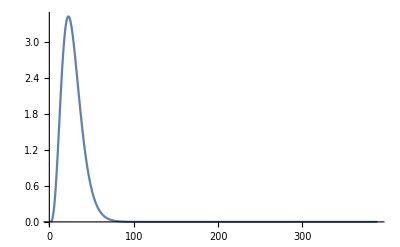

{1.444776941891850872364949,388.89528559119667744217}

-0.001232+0.00261308 ⅈ

6.58101×10^-9

7.51137×10^-6

```mathematica
TeukSource = TeukolskySource[RenormedData];
teuksourcemodalIntegrand = TeukolskySourceModalIntegrand[RenormedData,2,2, Source->TeukSource];
teuksourcemodal = TeukolskySourceModal[RenormedData,2,2, Recalculate->True, SourceIntegrand->teuksourcemodalIntegrand];
Print["TSmaxradialpoints: "<>ToString[$TSMaxRadialPoints]];
zinf = TeukolskyZInfinity[RenormedData,teuksourcemodal,2,2];
einf = EnergyFlux[RenormedData,2,2,TeukolskyTlmw->teuksourcemodal,ZCoefficient->zinf]
einf/(1-norm["FinalMass"])^2
```

```mathematica
(*TSMaxRadialPoints=300*)
6.169274915782216*^-6
```

```mathematica
(*TSMaxRadialPoints=150*)
0.000020258623586187822
```

```mathematica
(*TSMaxRadialPoints=100*)
0.00010961716109710625
```

#### Comparison of Data

```mathematica
mass = 0.2;
MySolution = getResults[$SolutionPath, {{"m", 1},{"n",0}, {"μNv", StringReplace[ToString[Rationalize[mass], InputForm], "/"->"_"]}}]//First;
```

```mathematica
Plot[MySolution["Solution", "R"][r]//ReIm, {r,1.44,10}]
```

#### Comparison of Norm

```mathematica
NormVal
```

0.0338697

#### Comparison of Vector Field

```mathematica
Aup = FKKSProca[MySolution, Optimized->True, QuasiboundState->True];
Adown = {t,r,θ,ϕ}|->Evaluate[Aup[t,r,θ,ϕ][{-ζ,-sphericalchart}]//ToBasis[sphericalchart]//ComponentArray//FromxActVariables//ApplyRealSolutionSet[RenormedData]];
```

```mathematica
Adown[0,2,2,0]*NormVal
```

{0.000595416,-0.0130383,0.00629153,-0.00278217}

#### Comparison of EM tensor

```mathematica
Tem = FKKSEnergyMomentum[RenormedData, Optimized->True, QuasiboundState->True];
```

nils tem

```mathematica
NilsTem = Function[{t,r,θ,ϕ},Block[{aa856,aa857,aa858,aa880,aa881,aa843,aa844,aa847,aa799,aa882,aa886,aa892,aa859,aa860,aa862,aa874,aa875,aa876,aa877,aa878,aa883,aa884,aa885,aa893,aa894,aa895,aa998,aa999,aa1004,aa853,aa896,aa897,aa898,aa992,aa993,aa994,aa995,aa1030,aa1031,aa1032,aa1033,aa1035,aa1036,aa1007,aa1008,aa1050,aa1051,aa1052,aa1053,aa1049,aa1006,aa854,aa1067,aa1068,aa1069,aa1070,aa1071,aa1075,aa1078,aa1079,aa1080,aa1081,aa1082,aa1083,aa1061,aa1086,aa1087,aa1088,aa1104,aa1105,aa1114,aa1038,aa1118,aa1119,aa1120,aa1108,aa1109,aa1110,aa1111,aa1112,aa1124,aa1125,aa1126,aa1127,aa1128,aa1134,aa1135,aa1136,aa1137,aa1138,aa1142,aa1143,aa1144,aa1145,aa1146,aa1150,aa1153,aa1154,aa1155,aa1011,aa1017,aa1018,aa1019,aa1020,aa1021,aa1023,aa1167,aa1168,aa1169,aa1170,aa1171,aa1162,aa1163,aa1164,aa1187,aa1012,aa1013,aa1014,aa1197,aa1209,aa1210,aa1009,aa1015,aa1028,aa1220,aa1122,aa1132,aa1140,aa1160,aa1165,aa1173,aa1177,aa1178,aa1179,aa1180,aa1181,aa1182,aa1183,aa1184,aa1185,aa1186,aa1188,aa1189,aa1190,aa1191,aa1192,aa1265,aa1193,aa1194,aa1195,aa1196,aa1198,aa1199,aa1200,aa1201,aa1202,aa1203,aa1204,aa1205,aa1206,aa1207,aa1208,aa1298,aa1299,aa1300,aa1301,aa1302,aa1303,aa1304,aa1305,aa1306,aa1307,aa1308,aa1309,aa1310,aa1311,aa1312,aa1313,aa1314,aa1315,aa1316,aa1277,aa1278,aa1211,aa1212,aa1213,aa1214,aa1215,aa1216,aa1217,aa1218,aa1219,aa1221,aa1222,aa1223,aa1224,aa1225,aa1226,aa1227,aa1228,aa1229,aa1230,aa1231,aa1232,aa1233,aa1234,aa1235,aa1236,aa1237,aa1238,aa1239,aa1240,aa1241,aa1242,aa1243,aa1244,aa1245,aa1246,aa1247,aa1248,aa1249,aa1250,aa1251,aa1252,aa1253,aa1254,aa1255,aa1256,aa1257,aa1258,aa1317,aa1318,aa1319,aa1320,aa1321,aa1322,aa1323,aa1324,aa1325,aa1326,aa1327,aa1328,aa1329,aa1330,aa1331,aa1368,aa1369,aa1370,aa1371,aa1372,aa1373,aa1374,aa1375,aa1376,aa1377,aa1378,aa1379,aa1380,aa1381,aa1382,aa1385,aa1386,aa1387,aa1388,aa1389,aa1390,aa1391,aa1395,aa1396,aa1383},aa856=0.28363236035996286959257196597021742589`25. t;aa857=-1.`25. ϕ;aa858=aa856+aa857;aa880=-2+r;aa881=aa880 r;aa843=Cos[θ];aa844=aa843^2;aa847=0.81`24.69897000433602 aa844;aa799=r^2;aa882=0.81`24.69897000433602+aa881;aa886=2 θ;aa892=Cos[aa886];aa859=Sin[aa858];aa860=InterpolatingFunction[…][r,θ];aa862=-0.00960666829530273561119407281670441763`19.999995657076894 aa859 aa860;aa874=Cos[aa858];aa875=InterpolatingFunction[…][r,θ];aa876=-0.00960666829530273561119407281670441763`19.999995657076894 aa874 aa875;aa877=aa862+aa876;aa878=aa877^2;aa883=1/aa882;aa884=aa881+aa847;aa885=2 aa799;aa893=0.81`24.69897000433602 aa892;aa894=0.81`24.69897000433602+aa885+aa893;aa895=1/aa894^3;aa998=0.03387014190873968730583669021891730935`19.999995657076894 aa859 aa860;aa999=0.03387014190873968730583669021891730935`19.999995657076894 aa874 aa875;aa1004=aa998+aa999;aa853=aa799+aa847;aa896=r^4;aa897=2 aa896;aa898=3 r;aa992=2+aa898;aa993=0.81`24.69897000433602 r aa992;aa994=0.81`24.69897000433602 aa882 aa892;aa995=0.6561`24.397940008672037+aa897+aa993+aa994;aa1030=InterpolatingFunction[…][r,θ];aa1031=-aa859 aa1030;aa1032=InterpolatingFunction[…][r,θ];aa1033=aa874 aa1032;aa1035=aa1031+aa1033;aa1036=aa1035^2;aa1007=Csc[θ];aa1008=aa1007^2;aa1050=0.03387014190873968730583669021891730935`19.999995657076894 aa874 aa1030;aa1051=0.03387014190873968730583669021891730935`19.999995657076894 aa859 aa1032;aa1052=aa1050+aa1051;aa1053=aa1052^2;aa1049=1/aa882^2;aa1006=aa884^2;aa854=1/aa853;aa1067=InterpolatingFunction[…][r,θ];aa1068=-0.03387014190873968730583669021891730935`20. aa859 aa1067;aa1069=InterpolatingFunction[…][r,θ];aa1070=0.03387014190873968730583669021891730935`20. aa874 aa1069;aa1071=aa1068+aa1070;aa1075=aa1071^2;aa1078=InterpolatingFunction[…][r,θ];aa1079=-0.03387014190873968730583669021891730935`20. aa859 aa1078;aa1080=InterpolatingFunction[…][r,θ];aa1081=0.03387014190873968730583669021891730935`20. aa874 aa1080;aa1082=aa1079+aa1081;aa1083=aa1082^2;aa1061=1/aa894;aa1086=InterpolatingFunction[…][r,θ];aa1087=-0.00960666829530273561119407281670441763`19.999995657076894 aa859 aa1086;aa1088=InterpolatingFunction[…][r,θ];aa1104=-0.00960666829530273561119407281670441763`19.999995657076894 aa874 aa1088;aa1105=aa1087+aa1104;aa1114=aa1105^2;aa1038=1/aa894^2;aa1118=aa874 aa1086;aa1119=-aa859 aa1088;aa1120=aa1118+aa1119;aa1108=Cot[θ];aa1109=0.81`24.69897000433602 aa843 aa1108;aa1110=aa880 r aa1007;aa1111=aa1109+aa1110;aa1112=aa1111^2;aa1124=InterpolatingFunction[…][r,θ];aa1125=0.03387014190873968730583669021891730935`20. aa874 aa1124;aa1126=InterpolatingFunction[…][r,θ];aa1127=-0.03387014190873968730583669021891730935`20. aa859 aa1126;aa1128=aa1125+aa1127;aa1134=InterpolatingFunction[…][r,θ];aa1135=0.03387014190873968730583669021891730935`20. aa874 aa1134;aa1136=InterpolatingFunction[…][r,θ];aa1137=-0.03387014190873968730583669021891730935`20. aa859 aa1136;aa1138=aa1135+aa1137;aa1142=InterpolatingFunction[…][r,θ];aa1143=-0.00960666829530273561119407281670441763`19.999995657076894 aa859 aa1142;aa1144=InterpolatingFunction[…][r,θ];aa1145=-0.00960666829530273561119407281670441763`19.999995657076894 aa874 aa1144;aa1146=aa1143+aa1145;aa1150=aa1146^2;aa1153=0.03387014190873968730583669021891730935`19.999995657076894 aa859 aa1142;aa1154=0.03387014190873968730583669021891730935`19.999995657076894 aa874 aa1144;aa1155=aa1153+aa1154;aa1011=1/aa853^2;aa1017=1/aa853^3;aa1018=InterpolatingFunction[…][r,θ];aa1019=0.03387014190873968730583669021891730935`20. aa874 aa1018;aa1020=InterpolatingFunction[…][r,θ];aa1021=-0.03387014190873968730583669021891730935`20. aa859 aa1020;aa1023=aa1019+aa1021;aa1167=InterpolatingFunction[…][r,θ];aa1168=0.03387014190873968730583669021891730935`20. aa874 aa1167;aa1169=InterpolatingFunction[…][r,θ];aa1170=-0.03387014190873968730583669021891730935`20. aa859 aa1169;aa1171=aa1168+aa1170;aa1162=aa874 aa1142;aa1163=-aa859 aa1144;aa1164=aa1162+aa1163;aa1187=aa894^2;aa1012=aa874 aa860;aa1013=-aa859 aa875;aa1014=aa1012+aa1013;aa1197=aa882^2;aa1209=Sin[θ];aa1210=aa1209^2;aa1009=aa1004^2;aa1015=aa1014^2;aa1028=aa1023^2;aa1220=r^3;aa1122=aa1120^2;aa1132=aa1128^2;aa1140=aa1138^2;aa1160=aa1155^2;aa1165=aa1164^2;aa1173=aa1171^2;aa1177=aa882 aa894 aa877 aa1023;aa1178=-aa882 aa894 aa1023 aa1071;aa1179=3.6`25. r aa853 aa1052 aa1082;aa1180=-3.6`25. r aa853 aa1082 aa1105;aa1181=-2 aa884 aa853 aa1008 aa1052 aa1138;aa1182=2 aa884 aa853 aa1008 aa1105 aa1138;aa1183=-3.6`25. r aa853 aa1052 aa1146;aa1184=3.6`25. r aa853 aa1105 aa1146;aa1185=2 aa884 aa853 aa1008 aa1052 aa1155;aa1186=-2 aa884 aa853 aa1008 aa1105 aa1155;aa1188=0.00005162339308131739906146712113029517`19.698965661412913 aa882 aa1187 aa1035 aa1164;aa1189=-aa882 aa894 aa877 aa1171;aa1190=aa882 aa894 aa1071 aa1171;aa1191=aa1177+aa1178+aa1179+aa1180+aa1181+aa1182+aa1183+aa1184+aa1185+aa1186+aa1188+aa1189+aa1190;aa1192=2 aa883 aa1038 aa1191;aa1265=1/aa882^3;aa1193=0.00005162339308131739906146712113029517`19.698965661412913 aa882 aa1187 aa1014 aa1035;aa1194=-3.6`25. r aa853 aa877 aa1052;aa1195=2 aa884 aa853 aa1008 aa1004 aa1052;aa1196=3.6`25. r aa853 aa1052 aa1071;aa1198=aa1197 aa894 aa1023 aa1082;aa1199=3.6`25. r aa853 aa877 aa1105;aa1200=-2 aa884 aa853 aa1008 aa1004 aa1105;aa1201=-3.6`25. r aa853 aa1071 aa1105;aa1202=-2 aa884 aa853 aa1008 aa1052 aa1128;aa1203=2 aa884 aa853 aa1008 aa1105 aa1128;aa1204=-aa1197 aa894 aa1023 aa1146;aa1205=-aa1197 aa894 aa1082 aa1171;aa1206=aa1197 aa894 aa1146 aa1171;aa1207=aa1193+aa1194+aa1195+aa1196+aa1198+aa1199+aa1200+aa1201+aa1202+aa1203+aa1204+aa1205+aa1206;aa1208=2 aa883 aa1038 aa1207;aa1298=aa995 aa877 aa1082;aa1299=3.6`25. r aa1004 aa1082;aa1300=-aa995 aa1071 aa1082;aa1301=-3.6`25. r aa1082 aa1128;aa1302=3.6`25. r aa877 aa1138;aa1303=-2 aa884 aa1008 aa1004 aa1138;aa1304=-3.6`25. r aa1071 aa1138;aa1305=2 aa884 aa1008 aa1128 aa1138;aa1306=-aa995 aa877 aa1146;aa1307=-3.6`25. r aa1004 aa1146;aa1308=aa995 aa1071 aa1146;aa1309=3.6`25. r aa1128 aa1146;aa1310=-3.6`25. r aa877 aa1155;aa1311=2 aa884 aa1008 aa1004 aa1155;aa1312=3.6`25. r aa1071 aa1155;aa1313=-2 aa884 aa1008 aa1128 aa1155;aa1314=0.00010324678616263479812293424226059035`19.698965661412913 aa882 aa894 aa1014 aa1164;aa1315=aa1298+aa1299+aa1300+aa1301+aa1302+aa1303+aa1304+aa1305+aa1306+aa1307+aa1308+aa1309+aa1310+aa1311+aa1312+aa1313+aa1314;aa1316=aa883 aa1061 aa1315;aa1277=2 aa880 r;aa1278=0.81`24.69897000433602+aa1277+aa893;aa1211=-3.6`25. r aa883 aa895 aa995 aa1210 aa878;aa1212=aa854 aa877 aa1004;aa1213=-25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa883 aa895 aa1210 aa877 aa1004;aa1214=7.19999999999999999999999999999999999999`25. r aa883 aa884 aa895 aa1009;aa1215=0.00009292210754637131831064081803453131`19.69896348996765 r aa1011 aa1210 aa1015;aa1216=0.9`25. r aa882 aa1017 aa1210 aa1028;aa1217=-0.00018584421509274263662128163606906263`19.69896348996765 r aa883 aa1038 aa995 aa1210 aa1036;aa1218=3.6`25. r aa883 aa1061 aa1053;aa1219=-3.6`25. r aa1049 aa884 aa895 aa995 aa1053;aa1221=-23.32799999999999999999999999999999999996`24.522878745280334 aa1220 aa1049 aa895 aa1210 aa1053;aa1222=7.19999999999999999999999999999999999999`25. r aa883 aa895 aa995 aa1210 aa877 aa1071;aa1223=-aa854 aa1004 aa1071;aa1224=25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa883 aa895 aa1210 aa1004 aa1071;aa1225=-3.6`25. r aa883 aa895 aa995 aa1210 aa1075;aa1226=-3.6`25. r aa895 aa995 aa1210 aa1083;aa1227=-7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa1052 aa1105;aa1228=7.19999999999999999999999999999999999999`25. r aa1049 aa884 aa895 aa995 aa1052 aa1105;aa1229=46.65599999999999999999999999999999999992`24.522878745280334 aa1220 aa1049 aa895 aa1210 aa1052 aa1105;aa1230=3.6`25. r aa883 aa1061 aa1114;aa1231=-3.6`25. r aa1049 aa884 aa895 aa995 aa1114;aa1232=-23.32799999999999999999999999999999999996`24.522878745280334 aa1220 aa1049 aa895 aa1210 aa1114;aa1233=0.00010324678616263479812293424226059035`19.698965661412913 aa1035 aa1120;aa1234=-0.00133807834866774698367322777969725092`19.698961318533236 aa799 aa883 aa1038 aa1210 aa1035 aa1120;aa1235=0.00037168843018548527324256327213812526`19.69896348996765 r aa883 aa884 aa1038 aa1122;aa1236=-aa854 aa877 aa1128;aa1237=25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa883 aa895 aa1210 aa877 aa1128;aa1238=-14.39999999999999999999999999999999999998`25. r aa883 aa884 aa895 aa1004 aa1128;aa1239=aa854 aa1071 aa1128;aa1240=-25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa883 aa895 aa1210 aa1071 aa1128;aa1241=7.19999999999999999999999999999999999999`25. r aa883 aa884 aa895 aa1132;aa1242=aa882 aa854 aa1082 aa1138;aa1243=-25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa895 aa1210 aa1082 aa1138;aa1244=7.19999999999999999999999999999999999999`25. r aa884 aa895 aa1140;aa1245=7.19999999999999999999999999999999999999`25. r aa895 aa995 aa1210 aa1082 aa1146;aa1246=-aa882 aa854 aa1138 aa1146;aa1247=25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa895 aa1210 aa1138 aa1146;aa1248=-3.6`25. r aa895 aa995 aa1210 aa1150;aa1249=-aa882 aa854 aa1082 aa1155;aa1250=25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa895 aa1210 aa1082 aa1155;aa1251=-14.39999999999999999999999999999999999998`25. r aa884 aa895 aa1138 aa1155;aa1252=aa882 aa854 aa1146 aa1155;aa1253=-25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa895 aa1210 aa1146 aa1155;aa1254=7.19999999999999999999999999999999999999`25. r aa884 aa895 aa1160;aa1255=0.00009292210754637131831064081803453131`19.69896348996765 r aa882 aa1011 aa1210 aa1165;aa1256=-1.8`25. r aa882 aa1017 aa1210 aa1023 aa1171;aa1257=0.9`25. r aa882 aa1017 aa1210 aa1173;aa1258=aa1211+aa1212+aa1213+aa1214+aa1215+aa1216+aa1217+aa1218+aa1219+aa1221+aa1222+aa1223+aa1224+aa1225+aa1226+aa1227+aa1228+aa1229+aa1230+aa1231+aa1232+aa1233+aa1234+aa1235+aa1236+aa1237+aa1238+aa1239+aa1240+aa1241+aa1242+aa1243+aa1244+aa1245+aa1246+aa1247+aa1248+aa1249+aa1250+aa1251+aa1252+aa1253+aa1254+aa1255+aa1256+aa1257;aa1317=aa882 aa894 aa1004 aa1023;aa1318=-aa853 aa995 aa1052 aa1082;aa1319=aa853 aa995 aa1082 aa1105;aa1320=-aa882 aa894 aa1023 aa1128;aa1321=-3.6`25. r aa853 aa1052 aa1138;aa1322=3.6`25. r aa853 aa1105 aa1138;aa1323=aa853 aa995 aa1052 aa1146;aa1324=-aa853 aa995 aa1105 aa1146;aa1325=3.6`25. r aa853 aa1052 aa1155;aa1326=-3.6`25. r aa853 aa1105 aa1155;aa1327=0.00005162339308131739906146712113029517`19.698965661412913 aa882 aa1187 aa1120 aa1164;aa1328=-aa882 aa894 aa1004 aa1171;aa1329=aa882 aa894 aa1128 aa1171;aa1330=aa1317+aa1318+aa1319+aa1320+aa1321+aa1322+aa1323+aa1324+aa1325+aa1326+aa1327+aa1328+aa1329;aa1331=2 aa883 aa1038 aa1330;aa1368=aa853 aa995 aa877 aa1052;aa1369=3.6`25. r aa853 aa1004 aa1052;aa1370=-aa853 aa995 aa1052 aa1071;aa1371=-aa853 aa995 aa877 aa1105;aa1372=-3.6`25. r aa853 aa1004 aa1105;aa1373=aa853 aa995 aa1071 aa1105;aa1374=0.00005162339308131739906146712113029517`19.698965661412913 aa882 aa1187 aa1014 aa1120;aa1375=-3.6`25. r aa853 aa1052 aa1128;aa1376=3.6`25. r aa853 aa1105 aa1128;aa1377=aa1197 aa894 aa1023 aa1138;aa1378=-aa1197 aa894 aa1023 aa1155;aa1379=-aa1197 aa894 aa1138 aa1171;aa1380=aa1197 aa894 aa1155 aa1171;aa1381=aa1368+aa1369+aa1370+aa1371+aa1372+aa1373+aa1374+aa1375+aa1376+aa1377+aa1378+aa1379+aa1380;aa1382=2 aa883 aa1038 aa1381;aa1385=0.81`24.69897000433602+aa799;aa1386=0.81`24.69897000433602 aa1385 aa844;aa1387=0.81`24.69897000433602 r;aa1388=1.62`24.69897000433602 aa1210;aa1389=aa1387+aa1220+aa1388;aa1390=r aa1389;aa1391=aa1386+aa1390;aa1395=1.62`24.69897000433602 r aa854 aa1210;aa1396=0.81`24.69897000433602+aa799+aa1395;aa1383=aa995^2;{{1/2 (2 aa854 aa878-4 aa883 aa884 aa895 aa995 aa878-28.79999999999999999999999999999999999996`25. r aa883 aa884 aa895 aa877 aa1004+8 aa883 aa1006 aa895 aa1008 aa1009+0.00010324678616263479812293424226059035`19.698965661412913 aa884 aa1011 aa1015+aa882 aa884 aa1017 aa1028+0.0002064935723252695962458684845211807`19.698965661412913 aa1036-0.0002064935723252695962458684845211807`19.698965661412913 aa883 aa884 aa1038 aa995 aa1036-25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa1049 aa884 aa895 aa1053+4 aa883 aa884 aa1061 aa1008 aa1053-4 aa1049 aa1006 aa895 aa995 aa1008 aa1053-4 aa854 aa877 aa1071+8 aa883 aa884 aa895 aa995 aa877 aa1071+28.79999999999999999999999999999999999996`25. r aa883 aa884 aa895 aa1004 aa1071+2 aa854 aa1075-4 aa883 aa884 aa895 aa995 aa1075+2 aa882 aa854 aa1083-4 aa884 aa895 aa995 aa1083+51.83999999999999999999999999999999999993`24.69897000433602 aa799 aa1049 aa884 aa895 aa1052 aa1105-8 aa883 aa884 aa1061 aa1008 aa1052 aa1105+8 aa1049 aa895 aa995 aa1112 aa1052 aa1105-25.91999999999999999999999999999999999997`24.69897000433602 aa799 aa1049 aa884 aa895 aa1114+4 aa883 aa884 aa1061 aa1008 aa1114-4 aa1049 aa1006 aa895 aa995 aa1008 aa1114-0.00148675372074194109297025308855250103`19.69896348996765 r aa883 aa884 aa1038 aa1035 aa1120+0.0004129871446505391924917369690423614`19.698965661412913 aa883 aa1006 aa1038 aa1008 aa1122+28.79999999999999999999999999999999999996`25. r aa883 aa884 aa895 aa877 aa1128-16 aa883 aa895 aa1112 aa1004 aa1128-28.79999999999999999999999999999999999996`25. r aa883 aa884 aa895 aa1071 aa1128+8 aa883 aa1006 aa895 aa1008 aa1132-28.79999999999999999999999999999999999996`25. r aa884 aa895 aa1082 aa1138+8 aa1006 aa895 aa1008 aa1140-4 aa882 aa854 aa1082 aa1146+8 aa884 aa895 aa995 aa1082 aa1146+28.79999999999999999999999999999999999996`25. r aa884 aa895 aa1138 aa1146+2 aa882 aa854 aa1150-4 aa884 aa895 aa995 aa1150+28.79999999999999999999999999999999999996`25. r aa884 aa895 aa1082 aa1155-16 aa895 aa1112 aa1138 aa1155-28.79999999999999999999999999999999999996`25. r aa884 aa895 aa1146 aa1155+8 aa1006 aa895 aa1008 aa1160+0.00010324678616263479812293424226059035`19.698965661412913 aa882 aa884 aa1011 aa1165-2 aa882 aa884 aa1017 aa1023 aa1171+aa882 aa884 aa1017 aa1173),aa1192,aa1208,aa1258},{aa1192,1/2 (aa1049 aa1061 aa995 aa878+7.19999999999999999999999999999999999999`25. r aa1049 aa1061 aa877 aa1004-2 aa1049 aa884 aa1061 aa1008 aa1009-0.00010324678616263479812293424226059035`19.698965661412913 aa883 aa1015+aa854 aa1028+0.00005162339308131739906146712113029517`19.698965661412913 aa1049 aa995 aa1036+6.47999999999999999999999999999999999999`24.69897000433602 aa799 aa1265 aa1061 aa1053+2 aa1265 aa884 aa853 aa1038 aa995 aa1008 aa1053-2 aa1049 aa1061 aa995 aa877 aa1071-7.19999999999999999999999999999999999999`25. r aa1049 aa1061 aa1004 aa1071+aa1049 aa1061 aa995 aa1075-aa883 aa1061 aa995 aa1083-12.95999999999999999999999999999999999998`24.69897000433602 aa799 aa1265 aa1061 aa1052 aa1105-4 aa1265 aa884 aa853 aa1038 aa995 aa1008 aa1052 aa1105+6.47999999999999999999999999999999999999`24.69897000433602 aa799 aa1265 aa1061 aa1114+2 aa1265 aa884 aa853 aa1038 aa995 aa1008 aa1114+0.00037168843018548527324256327213812526`19.69896348996765 r aa1049 aa1035 aa1120-0.00005162339308131739906146712113029517`19.698965661412913 aa1049 aa1278 aa1008 aa1122-7.19999999999999999999999999999999999999`25. r aa1049 aa1061 aa877 aa1128+4 aa1049 aa884 aa1061 aa1008 aa1004 aa1128+7.19999999999999999999999999999999999999`25. r aa1049 aa1061 aa1071 aa1128-2 aa1049 aa884 aa1061 aa1008 aa1132-7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa1082 aa1138+2 aa883 aa884 aa1061 aa1008 aa1140+2 aa883 aa1061 aa995 aa1082 aa1146+7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa1138 aa1146-aa883 aa1061 aa995 aa1150+7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa1082 aa1155-4 aa883 aa884 aa1061 aa1008 aa1138 aa1155-7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa1146 aa1155+2 aa883 aa884 aa1061 aa1008 aa1160+0.00010324678616263479812293424226059035`19.698965661412913 aa1165-2 aa854 aa1023 aa1171+aa854 aa1173),aa1316,aa1331},{aa1208,aa1316,1/2 (-aa883 aa1061 aa995 aa878-7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa877 aa1004+2 aa883 aa884 aa1061 aa1008 aa1009+0.00010324678616263479812293424226059035`19.698965661412913 aa1015+aa882 aa854 aa1028+0.00005162339308131739906146712113029517`19.698965661412913 aa883 aa995 aa1036+6.47999999999999999999999999999999999999`24.69897000433602 aa799 aa1049 aa1061 aa1053+2 aa1049 aa884 aa853 aa1038 aa995 aa1008 aa1053+2 aa883 aa1061 aa995 aa877 aa1071+7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa1004 aa1071-aa883 aa1061 aa995 aa1075+aa1061 aa995 aa1083-12.95999999999999999999999999999999999998`24.69897000433602 aa799 aa1049 aa1061 aa1052 aa1105-4 aa1049 aa884 aa853 aa1038 aa995 aa1008 aa1052 aa1105+6.47999999999999999999999999999999999999`24.69897000433602 aa799 aa1049 aa1061 aa1114+2 aa1049 aa884 aa853 aa1038 aa995 aa1008 aa1114+0.00037168843018548527324256327213812526`19.69896348996765 r aa883 aa1035 aa1120-0.00005162339308131739906146712113029517`19.698965661412913 aa883 aa1278 aa1008 aa1122+7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa877 aa1128-4 aa883 aa884 aa1061 aa1008 aa1004 aa1128-7.19999999999999999999999999999999999999`25. r aa883 aa1061 aa1071 aa1128+2 aa883 aa884 aa1061 aa1008 aa1132+7.19999999999999999999999999999999999999`25. r aa1061 aa1082 aa1138-2 aa884 aa1061 aa1008 aa1140-2 aa1061 aa995 aa1082 aa1146-7.19999999999999999999999999999999999999`25. r aa1061 aa1138 aa1146+aa1061 aa995 aa1150-7.19999999999999999999999999999999999999`25. r aa1061 aa1082 aa1155+4 aa884 aa1061 aa1008 aa1138 aa1155+7.19999999999999999999999999999999999999`25. r aa1061 aa1146 aa1155-2 aa884 aa1061 aa1008 aa1160-0.00010324678616263479812293424226059035`19.698965661412913 aa882 aa1165-2 aa882 aa854 aa1023 aa1171+aa882 aa854 aa1173),aa1382},{aa1258,aa1331,aa1382,aa883 aa895 aa1383 aa1210 aa878+14.39999999999999999999999999999999999998`25. r aa883 aa895 aa1210 aa1391 aa877 aa1004+aa854 aa1009-4 aa883 aa884 aa895 aa1391 aa1009-0.00005162339308131739906146712113029517`19.698965661412913 aa854 aa1210 aa1396 aa1015-1/2 aa882 aa1011 aa1210 aa1396 aa1028+0.00005162339308131739906146712113029517`19.698965661412913 aa883 aa1038 aa1383 aa1210 aa1036-aa883 aa1061 aa995 aa1053+1/2 aa1049 aa1278 aa895 aa1383 aa1053+6.47999999999999999999999999999999999999`24.69897000433602 aa799 aa1049 aa1038 aa1210 aa1396 aa1053-2 aa883 aa895 aa1383 aa1210 aa877 aa1071-14.39999999999999999999999999999999999998`25. r aa883 aa895 aa1210 aa1391 aa1004 aa1071+aa883 aa895 aa1383 aa1210 aa1075+aa895 aa1383 aa1210 aa1083+2 aa883 aa1061 aa995 aa1052 aa1105-aa1049 aa1278 aa895 aa1383 aa1052 aa1105-12.95999999999999999999999999999999999998`24.69897000433602 aa799 aa1049 aa1038 aa1210 aa1396 aa1052 aa1105-aa883 aa1061 aa995 aa1114+1/2 aa1049 aa1278 aa895 aa1383 aa1114+6.47999999999999999999999999999999999999`24.69897000433602 aa799 aa1049 aa1038 aa1210 aa1396 aa1114+0.00037168843018548527324256327213812526`19.69896348996765 r aa883 aa1061 aa1210 aa1396 aa1035 aa1120+0.00010324678616263479812293424226059035`19.698965661412913 aa1122-0.00010324678616263479812293424226059035`19.698965661412913 aa883 aa884 aa1061 aa1396 aa1122-14.39999999999999999999999999999999999998`25. r aa883 aa895 aa1210 aa1391 aa877 aa1128-2 aa854 aa1004 aa1128+8 aa883 aa884 aa895 aa1391 aa1004 aa1128+14.39999999999999999999999999999999999998`25. r aa883 aa895 aa1210 aa1391 aa1071 aa1128+aa854 aa1132-4 aa883 aa884 aa895 aa1391 aa1132+14.39999999999999999999999999999999999998`25. r aa895 aa1210 aa1391 aa1082 aa1138+aa882 aa854 aa1140-4 aa884 aa895 aa1391 aa1140-2 aa895 aa1383 aa1210 aa1082 aa1146-14.39999999999999999999999999999999999998`25. r aa895 aa1210 aa1391 aa1138 aa1146+aa895 aa1383 aa1210 aa1150-14.39999999999999999999999999999999999998`25. r aa895 aa1210 aa1391 aa1082 aa1155-2 aa882 aa854 aa1138 aa1155+8 aa884 aa895 aa1391 aa1138 aa1155+14.39999999999999999999999999999999999998`25. r aa895 aa1210 aa1391 aa1146 aa1155+aa882 aa854 aa1160-4 aa884 aa895 aa1391 aa1160-0.00005162339308131739906146712113029517`19.698965661412913 aa882 aa854 aa1210 aa1396 aa1165+aa882 aa1011 aa1210 aa1396 aa1023 aa1171-1/2 aa882 aa1011 aa1210 aa1396 aa1173}}]];
```

```mathematica
Tem[1,1.6,0.5,1]
```

CTensor[{{4.71021×10^-8,7.30624×10^-7,5.4996×10^-7,1.58958×10^-7},{7.30624×10^-7,-0.0000204386,7.49953×10^-7,-3.28107×10^-6},{5.4996×10^-7,7.49953×10^-7,2.89819×10^-6,-2.69065×10^-6},{1.58958×10^-7,-3.28107×10^-6,-2.69065×10^-6,-3.66408×10^-7}},{-sphericalchart,-sphericalchart},0]

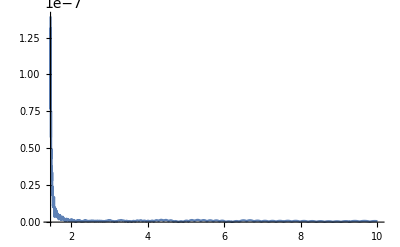

```mathematica
Plot[(NilsTem[1,r,0.5, 1]-Tem[1,r,0.5,1][[1]])//Norm, {r,1.46,10}, PlotRange->All]
```

#### Comparison of EM Projections

```mathematica
TNN = Tnn[RenormedData, AsInterpolatingFunction->True, ExtractTimeDependence->True];
NilsTNN ={r,θ}|->( ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]);
TMN = Tmbn[RenormedData, AsInterpolatingFunction->True, ExtractTimeDependence->True];
NilsTMN = {r,θ}|->(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]);
TMM = Tmbmb[RenormedData, AsInterpolatingFunction->True, ExtractTimeDependence->True];
NilsTMM = {r,θ}|->(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]);
```

```mathematica
GraphicsRow[{Plot3D[(TNN[r,θ]-NilsTNN[r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All, PlotLabel->"Tnn-NilsTnn"],
Plot3D[(TMN[r,θ]-NilsTMN[r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All, PlotLabel->"Tmn-NilsTmn"],
Plot3D[(TMM[r,θ]-NilsTMM[r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All, PlotLabel->"Tmm-NilsTmm"]}, ImageSize->1500]
GraphicsRow[{Plot3D[(Derivative[1,0][TNN][r,θ]-Derivative[1,0][NilsTNN][r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All,PlotLabel->"∂_r (Tnn-NilsTnn)"],
Plot3D[(Derivative[1,0][TMN][r,θ]-Derivative[1,0][NilsTMN][r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All,PlotLabel->"∂_r Tmn"],
Plot3D[(Derivative[1,0][TMM][r,θ]-Derivative[1,0][NilsTMM][r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All,PlotLabel->"∂_r Tmm"]}, ImageSize->1500]
GraphicsRow[{Plot3D[(Derivative[0,1][TNN][r,θ]-Derivative[0,1][NilsTNN][r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All,PlotLabel->"∂_θ Tnn"],
Plot3D[(Derivative[0,1][TMN][r,θ]-Derivative[0,1][NilsTMN][r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All,PlotLabel->"∂_θ Tmn"],
Plot3D[(Derivative[0,1][TMM][r,θ]-Derivative[0,1][NilsTMM][r,θ])//ReIm, {r,1.45, 20}, {θ,0.01,π-0.01}, PlotRange->All,PlotLabel->"∂_θ Tmm"]}, ImageSize->1500]
```

-Graphics-

-Graphics-

-Graphics-

#### Comparison of Teukolsky Source Term

Nils Teuk Source

```mathematica
NilsTeukSource[r_,θ_]:= 4 (r-0.9`25. ⅈ Cos[θ])^5 (r+0.9`25. ⅈ Cos[θ]) (-((-(r-0.9`25. ⅈ Cos[θ])^4 Cot[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))+2 (r-0.9`25. ⅈ Cos[θ])^4 Csc[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))+3.6`25. ⅈ (r-0.9`25. ⅈ Cos[θ])^3 Sin[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^4 Sin[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))+(r-0.9`25. ⅈ Cos[θ])^4 (1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) Sin[θ] (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))+2 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Cot[θ] Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Csc[θ] (1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))+1.8`25. ⅈ (0.9`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ]) (-0.9`25. ⅈ Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (Cos[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))-0.51053824864793316526662953874639136661`17.99999995657055 (1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (Cos[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.9`25. ⅈ (Cos[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))/(2 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ])))-((0.81`24.69897000433602-2 r+r^2)^2 (-(((r-0.9`25. ⅈ Cos[θ])^4 Cot[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2)+(2 (r-0.9`25. ⅈ Cos[θ])^4 Csc[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2+(3.6`25. ⅈ (r-0.9`25. ⅈ Cos[θ])^3 Sin[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2-(0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^4 Sin[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2+(r-0.9`25. ⅈ Cos[θ])^4 ((1.8`25. ⅈ Sin[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^3+(2 ((0.9`25. ⅈ (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r-0.9`25. ⅈ Cos[θ]) (-((1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))+((r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)))+ⅈ ((1.8`25. ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 (-((1.8`25. ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+((-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2))+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) Sin[θ] ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))+(r-0.9`25. ⅈ Cos[θ])^2 (2 (-((0.9`25. ⅈ Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))+((r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2))+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2))))/(r+0.9`25. ⅈ Cos[θ])^2)))/(2 √2 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ]))-((0.81`24.69897000433602-2 r+r^2)^2 ((4 (r-0.9`25. ⅈ Cos[θ])^3 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^4 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/((0.81`24.69897000433602-2 r+r^2)^2 (r+0.9`25. ⅈ Cos[θ])^2)+(r-0.9`25. ⅈ Cos[θ])^4 (-((2 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ])^3))+(-(((-2+2 r) (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/(0.81`24.69897000433602-2 r+r^2)^2)+(2 (r-0.9`25. ⅈ Cos[θ]) (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))-Cot[θ] (2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))+2 Csc[θ] (2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))+1.8`25. ⅈ ((r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ]) (2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))-0.51053824864793316526662953874639136661`17.99999995657055 (2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-1.8`25. ⅈ (Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))/(0.81`24.69897000433602-2 r+r^2))/(r+0.9`25. ⅈ Cos[θ])^2)))/(2 √2 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ]))-((0.81`24.69897000433602-2 r+r^2)^2 (4 (r-0.9`25. ⅈ Cos[θ])^3 ((2 (r-0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ]))+(r-0.9`25. ⅈ Cos[θ])^2 (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])))+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^4 ((2 (r-0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ]))+(r-0.9`25. ⅈ Cos[θ])^2 (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ]))))/(0.81`24.69897000433602-2 r+r^2)+(r-0.9`25. ⅈ Cos[θ])^4 (2 (r-0.9`25. ⅈ Cos[θ]) (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ]))+2 ((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])+(r-0.9`25. ⅈ Cos[θ]) (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])))+ⅈ ((2 (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ]))+(r-0.9`25. ⅈ Cos[θ])^2 (-(((-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ])^2))+(-(((-2+2 r) (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(1.13452944143985147837028786388086970358`18. r (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))/(r+0.9`25. ⅈ Cos[θ])))+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])^3-(2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])^2+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])))))/(4 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ])));
```

```mathematica
TeukSourceWithPre = OptimizedFunction[{R,Θ},(TeukSource[R,Θ]*(2/(Teukrhob * Teukrho^5))//FromxActVariables//ApplyRealSolutionSet[MySolution])/.{r->R, θ->Θ}//Evaluate];
NilsTeukSourceOE = OptimizedFunction[{r,θ}, Evaluate[NilsTeukSource[r,θ]]];
TeukSourceWithPre[3.86,0.1]
NilsTeukSourceOE[3.86,0.1]
```

```mathematica
Plot3D[(TeukSourceWithPre[r,θ]-NilsTeukSourceOE[r,θ])//ReIm, {r,1.45,40}, {θ,0.01,π-0.01}, PlotLabel->{"Re", "Im"},  PlotRange->All]
```

-Graphics3D-

#### Comparison of SWSH

```mathematica
Sqrt[2*π]*SpinWeightedSpheroidalHarmonicS[-2,2,2,χv*Re[2*ωv],#,0]&/@{0.001,π/4, π/2,π-0.01}
SWSHEigenvalue22 = SpinWeightedSpheroidalEigenvalue[-2,2,2,χv*2*Re[ωv]]
```

{1.76937,1.157104203448217,0.3077236407929939,5.45111×10^-10}

0.65781309036453777

#### Comparison of Teukolsky integrand

```mathematica
nilsteukint = {r,θ}|->4 (r-0.9`25. ⅈ Cos[θ])^5 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] InterpolatingFunction[…][θ] (-((-(r-0.9`25. ⅈ Cos[θ])^4 Cot[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))+2 (r-0.9`25. ⅈ Cos[θ])^4 Csc[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))+3.6`25. ⅈ (r-0.9`25. ⅈ Cos[θ])^3 Sin[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^4 Sin[θ] (2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])))+(r-0.9`25. ⅈ Cos[θ])^4 (1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) Sin[θ] (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))+2 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ]) Cot[θ] Csc[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Csc[θ] (1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))+1.8`25. ⅈ (0.9`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ]) (-0.9`25. ⅈ Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (Cos[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))-0.51053824864793316526662953874639136661`17.99999995657055 (1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ]) Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ]^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) (Cos[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))+(r-0.9`25. ⅈ Cos[θ])^2 (-0.9`25. ⅈ Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])-0.9`25. ⅈ (Cos[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+Sin[θ] (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))+(r+0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))))/(2 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ])))-((0.81`24.69897000433602-2 r+r^2)^2 (-(((r-0.9`25. ⅈ Cos[θ])^4 Cot[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2)+(2 (r-0.9`25. ⅈ Cos[θ])^4 Csc[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2+(3.6`25. ⅈ (r-0.9`25. ⅈ Cos[θ])^3 Sin[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2-(0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^4 Sin[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^2+(r-0.9`25. ⅈ Cos[θ])^4 ((1.8`25. ⅈ Sin[θ] ((2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))))/(r+0.9`25. ⅈ Cos[θ])^3+(2 ((0.9`25. ⅈ (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r-0.9`25. ⅈ Cos[θ]) (-((1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))+((r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)))+ⅈ ((1.8`25. ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2+(r-0.9`25. ⅈ Cos[θ])^2 (-((1.8`25. ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+((-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2))+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) Sin[θ] ((2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2)))+(r-0.9`25. ⅈ Cos[θ])^2 (2 (-((0.9`25. ⅈ Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))+((r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2))+(r+0.9`25. ⅈ Cos[θ])^2 (-(((-2+2 r) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])/(0.81`24.69897000433602-2 r+r^2))))/(r+0.9`25. ⅈ Cos[θ])^2)))/(2 √2 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ]))-((0.81`24.69897000433602-2 r+r^2)^2 ((4 (r-0.9`25. ⅈ Cos[θ])^3 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^4 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/((0.81`24.69897000433602-2 r+r^2)^2 (r+0.9`25. ⅈ Cos[θ])^2)+(r-0.9`25. ⅈ Cos[θ])^4 (-((2 (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ])^3))+(-(((-2+2 r) (-(r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Cot[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+2 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Csc[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+1.8`25. ⅈ (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-0.51053824864793316526662953874639136661`17.99999995657055 (r-0.9`25. ⅈ Cos[θ])^2 (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))))/(0.81`24.69897000433602-2 r+r^2)^2)+(2 (r-0.9`25. ⅈ Cos[θ]) (-1.8`25. ⅈ (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))-Cot[θ] (2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))+2 Csc[θ] (2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))+1.8`25. ⅈ ((r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ]) (2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))-0.51053824864793316526662953874639136661`17.99999995657055 (2 (r-0.9`25. ⅈ Cos[θ]) (r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ])^2 Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))+(r-0.9`25. ⅈ Cos[θ])^2 (2 (r+0.9`25. ⅈ Cos[θ]) (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])-1.8`25. ⅈ (Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])+(r+0.9`25. ⅈ Cos[θ]) Sin[θ] (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ]))+(r+0.9`25. ⅈ Cos[θ])^2 (InterpolatingFunction[…][r,θ]+ⅈ InterpolatingFunction[…][r,θ])))/(0.81`24.69897000433602-2 r+r^2))/(r+0.9`25. ⅈ Cos[θ])^2)))/(2 √2 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ]))-((0.81`24.69897000433602-2 r+r^2)^2 (4 (r-0.9`25. ⅈ Cos[θ])^3 ((2 (r-0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ]))+(r-0.9`25. ⅈ Cos[θ])^2 (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])))+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^4 ((2 (r-0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])+(ⅈ (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ])^2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ]))+(r-0.9`25. ⅈ Cos[θ])^2 (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ]))))/(0.81`24.69897000433602-2 r+r^2)+(r-0.9`25. ⅈ Cos[θ])^4 (2 (r-0.9`25. ⅈ Cos[θ]) (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ]))+2 ((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])+(r-0.9`25. ⅈ Cos[θ]) (-((ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])^2)+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])))+ⅈ ((2 (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (r-0.9`25. ⅈ Cos[θ]) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ]))+(r-0.9`25. ⅈ Cos[θ])^2 (-(((-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/((0.81`24.69897000433602-2 r+r^2) (r+0.9`25. ⅈ Cos[θ])^2))+(-(((-2+2 r) (-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2)^2)+(1.13452944143985147837028786388086970358`18. r (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])+(-1.8`25.+0.56726472071992573918514393194043485179`18. (0.81`24.69897000433602+r^2)) (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(0.81`24.69897000433602-2 r+r^2))/(r+0.9`25. ⅈ Cos[θ])))+(r-0.9`25. ⅈ Cos[θ])^2 ((2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])^3-(2 (ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ]))/(r+0.9`25. ⅈ Cos[θ])^2+(ⅈ InterpolatingFunction[…][r,θ]+InterpolatingFunction[…][r,θ])/(r+0.9`25. ⅈ Cos[θ])))))/(4 (r-0.9`25. ⅈ Cos[θ])^8 (r+0.9`25. ⅈ Cos[θ])));
```

0.0000905285-0.000120349 ⅈ
0.0000921904-0.000121017 ⅈ3.4254+0.0440698 ⅈ
3.42468+0.0426323 ⅈ6.8869×10^-18+2.48171×10^-18 ⅈ
8.87396×10^-20+3.37651×10^-20 ⅈ

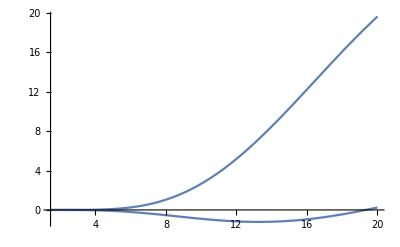

-Graphics3D-

```mathematica
With[{R1=3.86, θ1=0.001, R2=20,θ2=π/2, R3=1.5, θ3=π-0.01},
Row[{
Column[{teuksourcemodalIntegrand[R1,θ1],
nilsteukint[R1,θ1]}],Spacer[20],
Column[{
teuksourcemodalIntegrand[R2,θ2],
nilsteukint[R2,θ2]}],Spacer[20],
Column[{teuksourcemodalIntegrand[R3,θ3],
nilsteukint[R3,θ3]
}]
}]
]
Plot[teuksourcemodalIntegrand[r,1]//ReIm, {r,1.45,20}]
Plot3D[(teuksourcemodalIntegrand[r,θ]-nilsteukint[r,θ])//ReIm, {r,1.45,100}, {θ,0.001, π-0.001}, PlotRange->All]
```

#### Comparison of Tlmω

0.0269893-0.0434209 ⅈ

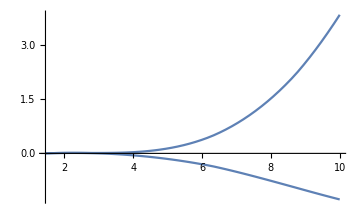
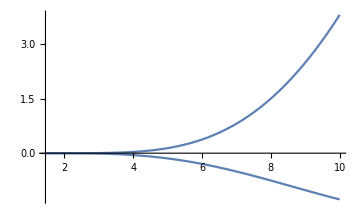
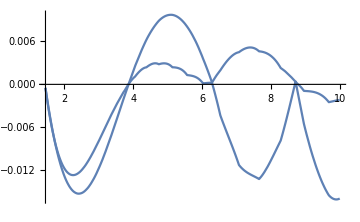

```mathematica
teuksourcemodal[3.86]
nilstlmw = InterpolatingFunction[…];
Column[{
Row[{
Plot[teuksourcemodal[r]//ReIm, {r,1.45,10},ImageSize->Medium],
Plot[(nilstlmw[r])//ReIm, {r,1.45,10},ImageSize->Medium]}],
Plot[(nilstlmw[r]-teuksourcemodal[r])//ReIm, {r,1.45,10}, ImageSize->Medium]
}]
```

#### Comparison of renormalized angular momentum

```mathematica
ClearAll[RenormedAngularMomentum]
```

```mathematica
RenormalizedAngularMomentum[-2,2,2,χv,2 SetPrecision[ωv//Re,64],Method->"Monodromy"]
RenormedAngMom=RenormedAngularMomentum[2 SetPrecision[ωv//Re,64],χv,2,2,-2];
```

1/2+0.708955468372856470403308835324087949755074195690432501 ⅈ

#### Comparison of Homogeneous solution of MST

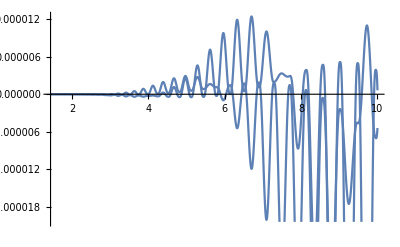

```mathematica
rdom = MySolution["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#, MySolution["Parameters", "χ"]]&;
TeukRin22 = RNumerical[RenormedAngMom,2*Re[ωv],χv,2,2,-2,SWSHEigenvalue22,rdom[[2]]];
nilsRinc = {r}|->(-3.487780249773632*^-32-1.271221319484332*^-31 ⅈ) InterpolatingFunction[…][r];
Plot[(nilsRinc[r]-TeukRin22[r])//ReIm, {r,1.44,10}]
```

#### Comparison of Z_lmω integrand

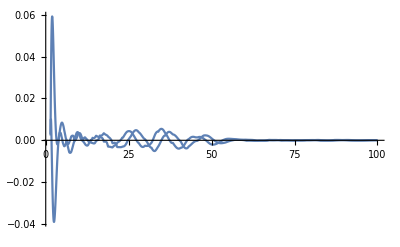

```mathematica
tlmw = {r}|->teuksourcemodal[r]//Evaluate;
rin = {r}|->TeukRin22[r]//Evaluate;
inte = {r}|->tlmw[r]*rin[r]/((0.9^2-2r+r^2)^2);
nilsint = {r}|->nilstlmw[r]*nilsRinc[r]/((0.9^2-2*r + r^2)^2);
Plot[(inte[r]-nilsint[r])//ReIm, {r,1.45,100},PlotRange->All]
```

#### Comparison of incoming amplitude

```mathematica
SWSHEigenvalue22 = SpinWeightedSpheroidalEigenvalue[-2,2,2,χv*2*Re[ωv]];
binc = IncomingAmplitudeB[RenormedAngMom,2*Re[ωv],χv,2,-2,SWSHEigenvalue22]
```

15.557757161322688710118753630928569873254279204802-1.268787801534708843875738653254601711094370572806 ⅈ

#### Comparison of Z_lmω

```mathematica
rdom =MySolution["Solution", "R"]["Domain"]//First//HorizonCoordToRadial[#, MySolution["Parameters", "χ"]]&;
integration = NIntegrate[inte[r], {r,2.5, 221.22222222222223866997073518750521560572`25.},
MaxRecursion->50,
WorkingPrecision->10]
integration/(2*2*Re[ωv]*I*binc)
```

-0.02616915311+0.02002314799 ⅈ

0.00100680078+0.00156471796 ⅈ

## Output data comparison

```mathematica
TestMass = 0.3;
$root = NotebookDirectory[]<>"../Debugging/NilsSiemonsenCode/OG_Code_MyExecution";
NilsSolutionGW = Import[$root<>"/GWoutput/GW_m1n0_a900000_mu30_prec25.mx"];
NilsSolution = NilsSolutionGW[[10]];
NilsSolution["Derived", "TotalEnergy"] = NilsSolutionGW[[5]];

(*Import my data*)
MySolution = getResults[$SolutionPath, {{"m", 1},{"n",0}, {"μNv", StringReplace[ToString[Rationalize[TestMass], InputForm], "/"->"_"]}}]//First;
MySolution["Derived"] = <|"Einf"->MySolution["Derived", "Einf"],"Tlmw"->MySolution["Derived","Tlmw"],"Normalization"->MySolution["Derived","Normalization", "Normalization"],"TotalEnergy"->MySolution["Derived","Normalization","TotalEnergy"],"FinalMass"->MySolution["Derived", "Normalization", "FinalMass"],"FinalSpin"->MySolution["Derived", "Normalization", "FinalSpin"],"Zinf"->MySolution["Derived", "Zinf"]|>;
MySolution["Derived"]["NormalizedEinf"] = MySolution["Derived", "Einf"]/(1-MySolution["Derived", "FinalMass"])^2;
```

```mathematica
DataToCompare = {{"Parameters", "μNv"}, {"Parameters", "m"}, {"Parameters", "n"},{"Solution", "ω"},{"Solution", "ν"},  {"Derived", "Einf"}, {"Derived", "NormalizedEinf"},{"Derived", "TotalEnergy"}, {"Derived", "FinalMass"}, {"Derived", "FinalSpin"}, {"Derived", "Normalization"}};
tabdata = Transpose@Table[ToString[ScientificForm@N@i[Sequence@@j], TraditionalForm], {i,{NilsSolution, MySolution}}, {j,DataToCompare}];
TableView[%, ImageSize->Large, Headers->{{"Nils", "Mine"}, DataToCompare[[All,2]]}, Alignment->Center, ItemSize->20, Scrollbars->False, HeaderSize->7]
```